```mathematica
generateSupergraph[structure_,graphDistribution_,edgeThickness_:1]:=Module[{clusters,g,previousCount=0,vertices,edges,connectingEdges},clusters=Table[Module[{cluster},cluster=IndexGraph[RandomGraph[graphDistribution],previousCount];
previousCount+=VertexCount[cluster];
{VertexList[cluster],EdgeList[cluster]}],{i,VertexCount[structure]}];
{vertices,edges}=Union@@@Transpose[clusters];
connectingEdges=UndirectedEdge@@RandomChoice@*First/@clusters[[{#1,#2}]]&@@@Catenate[ConstantArray[EdgeList[structure],edgeThickness]];
Graph[vertices,Join[edges,connectingEdges]]]
```

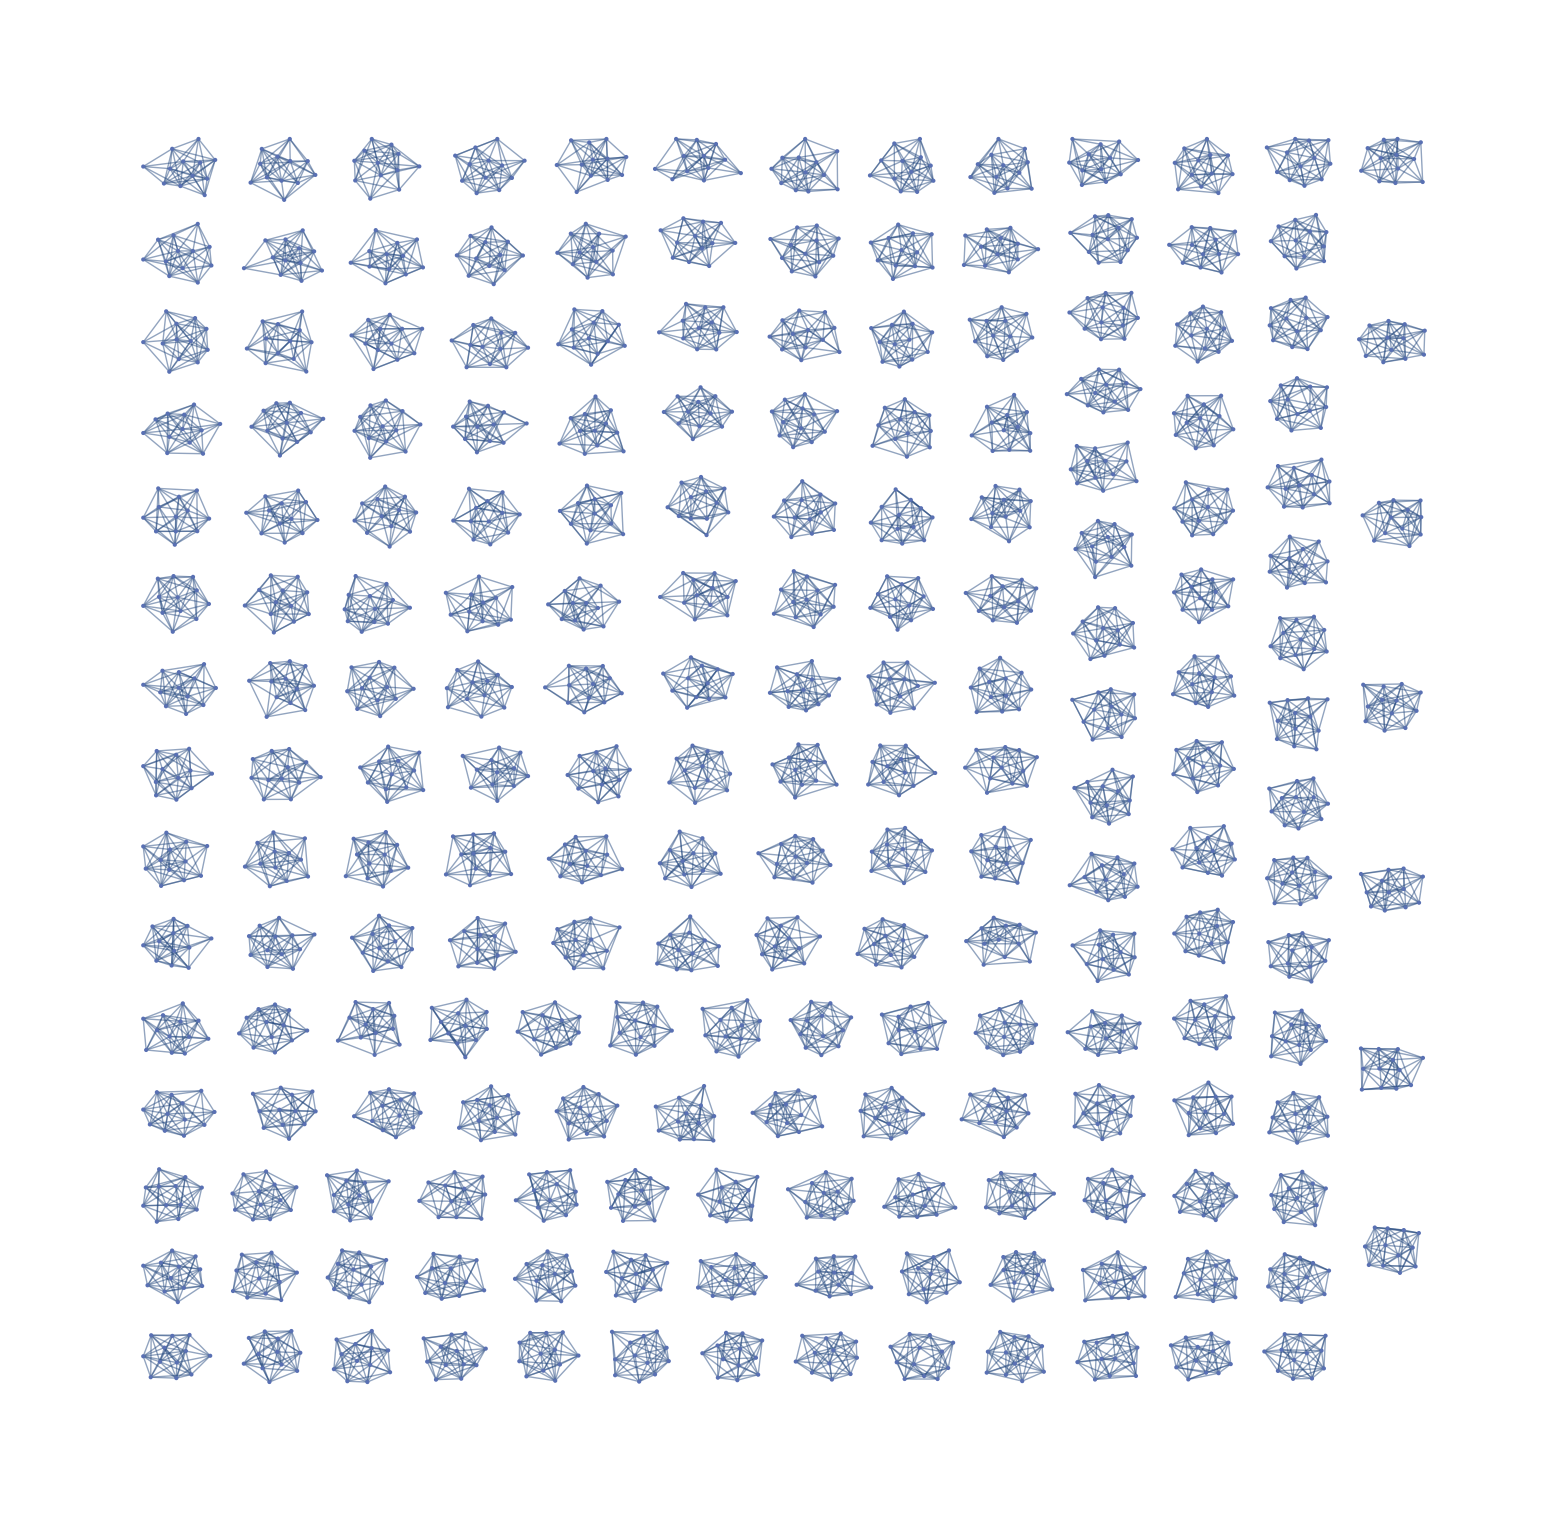

```mathematica
g=generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],193],WattsStrogatzGraphDistribution[12,0.2, 4],0]
```

```mathematica
agentNeighborhoods[g_] := Merge[Catenate[{#1->#2,#2->#1}&@@@EdgeList[g]],Identity]
```

```mathematica
neighbors=agentNeighborhoods[g]
```

<|0→{1,2,3,4,5,8,9,11},1→{0,2,4,5,8,7,10,11},2→{0,1,3,5,6,9,10,11},3→{0,2,4,5,6,7,10,11},4→{0,1,3,5,6,7,8},5→{1,2,3,4,0,6,8,9,7,10},8→{1,4,5,6,7,0,9,10,11},6→{2,3,4,5,7,8,9},9→{2,5,6,7,8,0,10,11},7→{3,4,6,1,5,8,9,10},10→{3,7,8,9,1,2,5,11},11→{8,9,10,0,1,2,3},12→{15,16,18,20,21,22,23},15→{12,13,14,16,17,19,20,23},16→{12,13,14,15,17,19,20},18→{12,14,17,19,20,21,22},13→{15,16,17,20,21,22,23},17→{13,14,15,16,18,19,20,21},14→{15,16,17,18,19,21,22,23},2279,2295→{2294,2292,2296,2297,2300,2301,2302},2298→{2294,2296,2297,2299,2300,2301,2302},2300→{2294,2295,2296,2297,2298,2299,2292,2293,2301,2303},2301→{2294,2297,2298,2299,2300,2293,2295,2302,2303},2302→{2298,2299,2301,2292,2293,2294,2295,2303},2303→{2299,2300,2301,2302,2292,2293,2294,2296},2304→{2305,2306,2308,2310,2312,2313,2314,2315},2305→{2304,2306,2307,2308,2310,2313,2314,2315},2306→{2304,2305,2307,2308,2309,2310,2312,2314,2315},2308→{2304,2305,2306,2307,2309,2310,2311,2312},2310→{2304,2305,2306,2308,2309,2311,2312,2313,2314},2307→{2305,2306,2308,2309,2311,2312,2315},2309→{2306,2307,2308,2310,2311,2312,2313,2315},2311→{2307,2308,2309,2310,2312,2313,2314,2315},2312→{2308,2309,2310,2311,2304,2306,2307,2313,2315},2313→{2309,2310,2311,2312,2304,2305,2314,2315},2315→{2309,2311,2312,2313,2304,2305,2306,2307},2314→{2310,2311,2313,2304,2305,2306}|>
 |  |  |  |

```mathematica
meetingCounts=AssociationThread[Keys[neighbors],ExponentialDistribution[2]]
```

<|0→ExponentialDistribution[2],1→ExponentialDistribution[2],2→ExponentialDistribution[2],3→ExponentialDistribution[2],4→ExponentialDistribution[2],5→ExponentialDistribution[2],8→ExponentialDistribution[2],6→ExponentialDistribution[2],9→ExponentialDistribution[2],7→ExponentialDistribution[2],10→ExponentialDistribution[2],11→ExponentialDistribution[2],12→ExponentialDistribution[2],15→ExponentialDistribution[2],16→ExponentialDistribution[2],18→ExponentialDistribution[2],13→ExponentialDistribution[2],17→ExponentialDistribution[2],14→ExponentialDistribution[2],19→ExponentialDistribution[2],20→ExponentialDistribution[2],2274,2296→ExponentialDistribution[2],2299→ExponentialDistribution[2],2297→ExponentialDistribution[2],2295→ExponentialDistribution[2],2298→ExponentialDistribution[2],2300→ExponentialDistribution[2],2301→ExponentialDistribution[2],2302→ExponentialDistribution[2],2303→ExponentialDistribution[2],2304→ExponentialDistribution[2],2305→ExponentialDistribution[2],2306→ExponentialDistribution[2],2308→ExponentialDistribution[2],2310→ExponentialDistribution[2],2307→ExponentialDistribution[2],2309→ExponentialDistribution[2],2311→ExponentialDistribution[2],2312→ExponentialDistribution[2],2313→ExponentialDistribution[2],2315→ExponentialDistribution[2],2314→ExponentialDistribution[2]|>
 |  |  |  |

```mathematica
recoveryTime=ExponentialDistribution[1/7];
```

```mathematica
agentStates=Join[AssociationThread[Keys[neighbors],"S"],
AssociationMap[{"I",Floor@RandomVariate[recoveryTime]}&,RandomSample[Keys[neighbors],3]]]
```

<|0→S,1→S,2→S,3→S,4→S,5→S,8→S,6→S,9→S,7→S,10→S,11→S,12→S,15→S,16→S,18→S,13→S,17→S,14→S,19→S,20→S,21→S,22→S,23→S,24→S,26→S,27→S,28→S,30→S,31→S,25→S,29→S,32→S,33→S,34→S,35→S,36→S,37→S,38→S,39→S,40→S,41→S,42→S,43→S,44→S,47→S,45→S,46→S,48→S,50→S,51→S,52→S,49→S,53→S,56→S,54→S,55→S,59→S,57→S,58→S,60→S,61→S,62→S,63→S,67→S,64→S,65→S,66→S,71→S,68→S,69→S,70→S,72→S,73→S,74→S,75→S,76→S,77→S,80→S,78→S,79→S,81→S,82→S,83→S,84→S,85→S,86→S,87→S,88→S,90→S,89→S,91→S,93→S,94→S,92→S,95→S,96→S,98→S,100→S,102→S,97→S,99→S,101→S,104→S,106→S,103→S,105→S,107→S,108→S,109→S,110→S,111→S,112→S,115→S,113→S,114→S,116→S,117→S,119→S,118→S,120→S,121→S,123→S,124→S,126→S,125→S,128→S,122→S,127→S,129→S,130→S,131→S,132→S,133→S,134→S,135→S,136→S,137→S,138→S,139→S,140→S,141→S,142→S,143→S,144→S,145→S,146→S,148→S,150→S,147→S,149→S,151→S,152→S,153→S,154→S,155→S,156→S,157→S,158→S,159→S,161→S,163→S,160→S,162→S,165→S,166→S,164→S,167→S,168→S,169→S,172→S,173→S,174→S,170→S,171→S,176→S,175→S,177→S,178→S,179→S,180→S,181→S,183→S,184→S,182→S,185→S,186→S,189→S,187→S,188→S,190→S,191→S,192→S,193→S,194→S,195→S,196→S,197→S,198→S,199→S,202→S,200→S,201→S,203→S,204→S,207→S,208→S,210→S,205→S,209→S,206→S,211→S,212→S,215→S,213→S,214→S,216→S,217→S,218→S,219→S,220→S,221→S,223→S,222→S,225→S,224→S,226→S,227→S,228→S,229→S,230→S,231→S,232→S,233→S,235→S,234→S,237→S,236→S,239→S,238→S,240→S,241→S,242→S,243→S,244→S,245→S,246→S,248→S,249→S,247→S,250→S,251→S,252→S,253→S,254→S,255→S,256→S,257→S,258→S,260→S,259→S,261→S,262→S,263→S,264→S,266→S,267→S,268→S,265→S,269→S,270→S,271→S,272→S,273→S,274→S,275→S,276→S,277→S,278→S,281→S,279→S,280→S,282→S,283→S,284→S,285→S,287→S,286→S,288→S,289→S,290→S,291→S,292→S,293→S,294→S,295→S,296→S,297→S,298→S,299→S,300→S,302→S,303→S,304→S,301→S,305→S,306→S,309→S,307→S,308→S,310→S,311→S,312→S,313→S,314→S,316→S,317→S,318→S,315→S,319→S,320→S,321→S,322→S,323→S,324→S,325→S,327→S,328→S,329→S,326→S,331→S,330→S,332→S,333→S,334→S,335→S,336→S,337→S,338→S,339→S,340→S,341→S,342→S,343→S,344→S,347→S,345→S,346→S,348→S,349→S,351→S,352→S,355→S,350→S,353→S,354→S,358→S,356→S,357→S,359→S,360→S,361→S,362→S,364→S,365→S,367→S,363→S,366→S,368→S,369→S,371→S,370→S,372→S,373→S,374→S,375→S,376→S,377→S,378→S,381→S,379→S,380→S,382→S,383→S,384→S,385→S,386→S,387→S,388→S,389→S,390→S,391→S,392→S,393→S,394→S,395→S,396→S,397→S,399→S,400→S,401→S,403→S,398→S,402→S,405→S,406→S,404→S,407→S,408→S,410→S,411→S,412→S,415→S,409→S,413→S,414→S,416→S,419→S,417→S,418→S,420→S,421→S,424→S,425→S,422→S,423→S,426→S,428→S,429→S,427→S,430→S,431→S,432→S,433→S,434→S,435→S,436→S,437→S,440→S,438→S,439→S,441→S,442→S,443→S,444→S,445→S,447→S,448→S,450→S,446→S,449→S,451→S,452→S,453→S,454→S,455→S,456→S,457→S,458→S,459→S,460→S,461→S,464→S,462→S,463→S,466→S,465→S,467→S,468→S,469→S,470→S,471→S,472→S,475→S,473→S,474→S,478→S,476→S,477→S,479→S,480→S,482→S,483→S,484→S,487→S,481→S,485→S,486→S,488→S,489→S,491→S,490→S,492→S,493→S,494→S,495→S,496→S,500→S,497→S,498→S,499→S,501→S,502→S,503→S,504→S,506→S,508→S,509→S,505→S,507→S,510→S,511→S,512→S,513→S,515→S,514→S,516→S,517→S,518→S,520→S,523→S,521→S,522→S,519→{I,1},524→S,526→S,525→S,527→S,528→S,529→S,530→S,531→S,532→S,533→S,534→S,536→S,537→S,535→S,539→S,538→S,540→S,541→S,542→S,543→S,544→S,548→S,545→S,547→S,546→S,551→S,549→S,550→S,552→S,553→S,554→S,555→S,556→S,558→S,557→S,561→S,559→S,562→S,560→S,563→S,564→S,565→S,566→S,568→S,570→S,567→S,569→S,572→S,571→S,573→S,574→S,575→S,576→S,577→S,578→S,580→S,582→S,583→S,579→S,581→S,586→S,584→S,585→S,587→S,588→S,589→S,590→S,592→S,593→S,591→S,599→S,594→S,595→S,596→S,597→S,598→S,600→S,602→S,603→S,604→S,605→S,601→S,606→S,607→S,608→S,611→S,609→S,610→S,612→S,613→S,614→S,615→S,616→S,618→S,623→S,617→S,619→S,621→S,620→S,622→S,624→S,625→S,627→S,628→S,626→S,629→S,632→S,630→S,631→S,633→S,635→S,634→S,636→S,637→S,638→S,639→S,641→S,640→S,642→S,645→S,643→S,644→S,647→S,646→S,648→S,649→S,651→S,652→S,653→S,650→S,654→S,656→S,655→S,657→S,658→S,659→S,660→S,661→S,662→S,663→S,664→S,665→S,666→S,667→S,668→S,669→S,670→S,671→S,672→S,673→S,675→S,676→S,674→S,677→S,679→S,680→S,678→S,681→S,682→S,683→S,684→S,685→S,686→S,687→S,688→S,690→S,691→S,689→S,694→S,692→S,693→S,695→S,696→S,697→S,698→S,699→S,700→S,701→S,702→S,704→S,705→S,703→S,707→S,706→S,708→S,709→S,710→S,711→S,712→S,713→S,714→S,715→S,716→S,717→S,718→S,719→S,720→S,721→S,723→S,724→S,726→S,725→S,728→S,722→S,727→S,729→S,731→S,730→S,732→S,733→S,734→S,735→S,736→S,737→S,740→S,738→S,739→S,741→S,742→S,743→S,744→S,746→S,747→S,748→S,745→S,751→S,752→S,750→S,749→S,753→S,755→S,754→S,756→S,757→S,758→S,759→S,760→S,762→S,761→S,765→S,763→S,767→S,766→S,764→S,768→S,769→S,770→S,771→S,772→S,773→S,774→S,776→S,775→S,778→S,777→S,779→S,780→S,781→S,783→S,784→S,785→S,782→S,791→S,786→S,787→S,788→S,789→S,790→S,792→S,793→S,794→S,795→S,796→S,797→S,798→S,799→S,801→S,800→S,802→S,803→S,804→S,805→S,806→S,807→S,808→S,809→S,810→S,811→S,812→S,814→S,813→S,815→S,816→S,817→S,818→S,819→S,821→S,820→S,823→S,822→S,825→S,824→S,826→S,827→S,828→S,829→S,830→S,831→S,832→S,834→S,835→S,836→S,833→S,837→S,838→S,839→S,840→S,841→S,842→S,844→S,845→S,846→S,843→S,849→S,847→S,848→S,850→S,851→S,852→S,853→S,854→S,855→S,856→S,858→S,857→S,860→S,859→S,861→S,863→S,862→S,864→S,865→S,866→S,867→S,868→S,869→S,870→S,872→S,871→{I,4},873→S,874→S,875→S,876→S,878→S,879→S,880→S,881→S,877→S,882→S,883→S,884→S,885→S,886→S,887→S,888→S,889→S,890→S,891→S,892→S,894→S,899→S,893→S,895→S,896→S,897→S,898→S,900→S,901→S,902→S,903→S,904→S,907→S,905→S,910→S,906→S,909→S,908→S,911→S,912→S,913→S,914→S,915→S,916→S,917→S,918→S,921→S,919→S,920→S,922→S,923→S,924→S,926→S,928→S,930→S,925→S,927→S,929→S,931→S,932→S,935→S,933→S,934→S,936→S,937→S,938→S,939→S,940→S,941→S,942→S,943→S,944→S,947→S,945→S,946→S,948→S,949→S,950→S,951→S,952→S,955→S,953→S,954→S,957→S,958→S,956→S,959→S,960→S,961→S,963→S,966→S,969→S,962→S,964→S,965→S,968→S,967→S,970→S,971→S,972→S,973→S,974→S,976→S,975→S,977→S,978→S,979→S,981→S,980→S,982→S,983→S,984→S,985→S,986→S,987→S,988→S,989→S,990→S,992→S,991→S,993→S,994→S,995→S,996→S,997→S,998→S,999→S,1000→S,1001→S,1002→S,1003→S,1004→S,1007→S,1005→S,1006→S,1008→S,1009→S,1010→S,1011→S,1012→S,1014→S,1016→S,1013→S,1015→S,1017→S,1019→S,1018→S,1020→S,1021→S,1022→S,1023→S,1024→S,1025→S,1026→S,1028→S,1029→S,1027→S,1030→S,1031→S,1032→S,1034→S,1035→S,1033→S,1037→S,1036→S,1038→S,1039→S,1040→S,1042→S,1041→S,1043→S,1044→S,1045→S,1047→S,1048→S,1051→S,1046→S,1049→S,1050→S,1052→S,1053→S,1054→S,1055→S,1056→S,1057→S,1058→S,1059→S,1060→S,1061→S,1062→S,1064→S,1063→S,1066→S,1065→S,1067→S,1068→S,1069→S,1070→S,1072→S,1073→S,1071→S,1075→S,1074→S,1076→S,1077→S,1079→S,1078→S,1080→S,1081→S,1082→S,1083→S,1084→S,1085→S,1086→S,1089→S,1087→S,1090→S,1088→S,1091→S,1092→S,1093→S,1094→S,1095→S,1096→S,1098→S,1099→S,1097→S,1100→S,1101→S,1103→S,1102→S,1104→S,1105→S,1106→S,1108→S,1107→S,1109→S,1112→S,1115→S,1110→S,1113→S,1111→S,1114→S,1116→S,1117→S,1118→S,1120→S,1122→S,1119→S,1123→S,1121→S,1124→S,1125→S,1126→S,1127→S,1128→S,1129→S,1130→S,1132→S,1134→S,1131→S,1133→S,1135→S,1136→S,1137→S,1139→S,1138→S,1140→S,1142→S,1143→S,1141→S,1144→S,1145→S,1146→S,1147→S,1148→S,1149→S,1150→S,1151→S,1152→S,1153→S,1154→S,1155→S,1158→S,1156→S,1157→S,1159→S,1160→S,1161→S,1162→S,1163→S,1164→S,1165→S,1166→S,1167→S,1171→S,1168→S,1169→S,1170→S,1172→S,1173→S,1174→S,1175→S,1176→S,1177→S,1178→S,1180→S,1179→S,1181→S,1183→S,1182→S,1185→S,1184→S,1186→S,1187→S,1188→S,1190→S,1192→S,1193→S,1189→S,1191→S,1194→S,1195→S,1196→S,1197→S,1198→S,1199→S,1200→S,1201→S,1202→S,1203→S,1204→S,1205→S,1206→S,1207→S,1208→S,1209→S,1210→S,1211→S,1212→S,1213→S,1214→S,1215→S,1219→S,1216→S,1217→S,1220→S,1218→S,1221→S,1223→S,1222→S,1224→S,1225→S,1226→S,1227→S,1228→S,1231→S,1229→S,1230→S,1232→S,1233→S,1234→S,1235→S,1236→S,1237→S,1238→S,1239→S,1240→S,1241→S,1242→S,1244→S,1243→S,1245→S,1246→S,1247→S,1248→S,1250→S,1251→S,1252→S,1255→S,1249→S,1253→S,1254→S,1256→S,1259→S,1257→S,1258→S,1260→S,1261→S,1262→S,1263→S,1264→S,1265→S,1266→S,1268→S,1267→S,1269→S,1270→S,1271→S,1272→S,1273→S,1274→S,1275→S,1276→S,1278→S,1277→S,1279→S,1280→S,1281→S,1283→S,1282→S,1284→S,1285→S,1286→S,1287→S,1288→S,1289→S,1291→S,1290→S,1292→S,1293→S,1295→S,1294→S,1296→S,1298→S,1300→S,1301→S,1302→S,1297→S,1299→S,1303→S,1305→S,1304→S,1307→S,1306→S,1308→S,1309→S,1310→S,1311→S,1312→S,1315→S,1313→S,1314→S,1316→S,1317→S,1318→S,1319→S,1320→S,1321→S,1322→S,1324→S,1323→S,1325→S,1327→S,1326→S,1328→S,1329→S,1330→S,1331→S,1332→S,1333→S,1334→S,1335→S,1337→S,1338→S,1339→S,1336→S,1340→S,1341→S,1343→S,1342→S,1344→S,1345→S,1346→S,1347→S,1348→S,1353→S,1349→S,1350→S,1352→S,1351→S,1355→S,1354→S,1356→S,1357→S,1359→S,1360→S,1361→S,1358→S,1362→S,1363→S,1364→S,1365→S,1366→S,1367→S,1368→S,1369→S,1370→S,1371→S,1372→S,1373→S,1374→S,1375→S,1377→S,1376→S,1378→S,1379→S,1380→S,1381→S,1382→S,1383→S,1384→S,1385→S,1388→S,1386→S,1387→S,1390→S,1389→S,1391→S,1392→S,1393→S,1394→S,1395→S,1398→S,1396→S,1397→S,1399→S,1400→S,1401→S,1402→S,1403→S,1404→S,1406→S,1407→S,1408→S,1409→S,1411→S,1405→S,1412→S,1410→S,1413→S,1414→S,1415→S,1416→S,1417→S,1418→S,1419→S,1420→S,1421→S,1424→S,1422→S,1423→S,1426→S,1425→S,1427→S,1428→S,1429→S,1430→S,1431→S,1432→S,1433→S,1434→S,1435→S,1436→S,1437→S,1438→S,1439→S,1440→S,1441→S,1442→S,1443→S,1444→S,1445→S,1448→S,1446→S,1447→S,1451→S,1449→S,1450→S,1452→S,1453→S,1454→S,1455→S,1456→S,1463→S,1457→S,1459→S,1460→S,1458→S,1461→S,1462→S,1464→S,1465→S,1467→S,1468→S,1470→S,1466→S,1469→S,1471→S,1472→S,1473→S,1474→S,1475→S,1476→S,1477→S,1478→S,1479→S,1480→S,1483→S,1481→S,1482→S,1484→S,1485→S,1486→S,1487→S,1488→S,1489→S,1491→S,1492→S,1494→S,1495→S,1490→S,1493→S,1496→S,1499→S,1497→S,1498→S,1500→S,1501→S,1502→S,1503→S,1504→S,1505→S,1507→S,1506→S,1508→S,1509→S,1510→S,1511→S,1512→S,1513→S,1514→S,1515→S,1516→S,1522→S,1518→S,1517→S,1521→S,1519→S,1520→S,1523→S,1524→S,1525→S,1526→S,1527→S,1528→S,1529→S,1530→S,1531→S,1534→S,1535→S,1532→S,1533→S,1536→S,1537→S,1538→S,1539→S,1542→S,1541→S,1543→S,1547→S,1540→S,1544→S,1545→S,1546→S,1548→S,1550→S,1551→S,1552→S,1554→S,1549→S,1553→S,1555→S,1556→S,1559→S,1557→S,1558→S,1560→S,1561→S,1562→S,1563→S,1564→S,1567→S,1565→S,1566→S,1568→S,1569→S,1571→S,1570→S,1572→S,1573→S,1575→S,1576→S,1574→S,1577→S,1578→S,1580→S,1579→S,1583→S,1581→S,1582→S,1584→S,1585→S,1586→S,1587→S,1588→S,1589→S,1591→S,1590→S,1592→S,1593→S,1594→S,1595→S,1596→S,1597→S,1598→S,1599→S,1600→S,1601→S,1602→S,1604→S,1605→S,1607→S,1603→S,1606→S,1608→S,1609→S,1610→S,1611→S,1612→S,1613→S,1614→S,1615→S,1617→S,1618→S,1616→S,1619→S,1620→S,1621→S,1622→S,1623→S,1624→S,1626→S,1627→S,1625→S,1628→S,1629→S,1631→S,1630→S,1632→S,1633→S,1634→S,1635→S,1639→S,1640→S,1636→S,1638→S,1637→S,1641→S,1642→S,1643→S,1644→S,1645→S,1646→S,1647→S,1648→S,1649→S,1650→S,1651→S,1653→S,1652→S,1654→S,1655→S,1656→S,1657→S,1660→S,1661→S,1662→S,1658→S,1659→S,1663→S,1666→S,1664→S,1665→S,1667→S,1668→S,1670→S,1671→S,1672→S,1679→S,1669→S,1673→S,1675→S,1677→S,1674→S,1676→S,1678→S,1680→S,1681→S,1682→S,1683→S,1686→S,1684→S,1685→S,1687→S,1688→S,1689→S,1691→S,1690→S,1692→S,1693→S,1694→S,1695→S,1696→S,1697→S,1698→S,1700→S,1699→S,1703→S,1701→S,1702→S,1704→S,1705→S,1706→S,1707→S,1708→S,1709→S,1710→S,1711→S,1712→S,1715→S,1713→S,1714→S,1716→S,1717→S,1719→S,1721→S,1723→S,1718→S,1720→S,1722→S,1724→S,1727→S,1725→S,1726→S,1728→S,1729→S,1731→S,1732→S,1733→S,1735→S,1736→S,1730→S,1734→S,1737→S,1738→S,1739→S,1740→S,1741→S,1742→S,1743→S,1744→S,1745→S,1746→S,1747→S,1748→S,1749→S,1750→S,1751→S,1752→S,1753→S,1754→S,1755→S,1756→S,1759→S,1757→S,1758→S,1761→S,1760→S,1762→S,1763→S,1764→S,1765→S,1766→S,1767→S,1768→S,1769→S,1770→S,1771→S,1772→S,1773→S,1774→S,1775→S,1776→S,1778→S,1779→S,1777→S,1780→S,1781→S,1782→S,1784→S,1783→S,1786→S,1785→S,1787→S,1788→S,1789→S,1791→S,1792→S,1790→S,1795→S,1796→S,1793→S,1794→S,1797→S,1798→S,1799→S,1800→S,1801→S,1802→S,1803→S,1804→S,1805→S,1806→S,1807→S,1810→S,1808→S,1809→S,1811→S,1812→S,1813→S,1814→S,1815→S,1816→S,1819→S,1817→S,1818→S,1820→S,1821→S,1823→S,1822→S,1824→S,1825→S,1826→S,1828→S,1827→S,1829→S,1830→S,1831→S,1832→S,1833→S,1834→S,1835→S,1836→S,1837→S,1838→S,1839→S,1840→S,1842→S,1841→S,1844→S,1845→S,1843→S,1846→S,1847→S,1848→S,1849→S,1851→S,1852→S,1855→S,1850→S,1853→S,1856→S,1854→S,1857→S,1858→S,1859→S,1860→S,1862→S,1864→S,1861→S,1865→S,1868→S,1863→S,1866→S,1869→S,1867→S,1870→S,1871→S,1872→S,1873→S,1874→S,1875→S,1876→S,1877→S,1878→S,1879→S,1880→S,1881→S,1882→S,1883→S,1884→S,1885→S,1886→S,1887→S,1890→S,1888→S,1889→S,1891→S,1892→S,1893→S,1894→S,1895→S,1896→S,1897→S,1898→S,1899→S,1900→S,1901→S,1902→S,1903→S,1904→S,1905→S,1906→S,1907→S,1908→S,1909→S,1911→S,1912→S,1919→S,1910→S,1913→S,1914→S,1915→S,1916→S,1917→S,1918→S,1920→S,1921→S,1923→S,1924→S,1927→S,1922→S,1928→S,1925→S,1926→S,1931→S,1929→S,1930→S,1932→S,1934→S,1935→S,1936→S,1933→S,1940→S,1937→S,1938→S,1939→S,1941→S,1942→S,1943→S,1944→S,1945→S,1946→S,1947→S,1948→S,1951→S,1949→S,1950→S,1952→S,1953→S,1954→S,1955→S,1956→S,1957→S,1958→S,1959→S,1960→S,1961→S,1962→S,1963→S,1964→S,1965→S,1966→S,1967→S,1968→S,1969→S,1970→S,1971→S,1972→S,1973→S,1974→S,1975→S,1976→S,1977→S,1979→S,1978→S,1980→S,1981→S,1982→S,1983→S,1984→S,1985→S,1988→S,1986→S,1987→S,1989→S,1991→S,1990→S,1992→S,1993→S,1995→S,1996→S,1998→S,1994→S,1997→S,1999→S,2000→S,2001→S,2002→S,2003→S,2004→S,2005→S,2006→S,2007→S,2008→S,2009→S,2011→S,2010→S,2012→S,2014→S,2013→S,2015→S,2016→S,2017→S,2018→S,2019→S,2020→S,2021→S,2023→S,2022→S,2024→S,2025→S,2026→S,2027→S,2028→S,2029→S,2030→S,2031→S,2032→S,2036→S,2033→S,2034→S,2035→S,2037→S,2038→S,2039→S,2040→S,2041→S,2042→S,2043→S,2044→S,2047→S,2045→S,2046→S,2050→S,2051→S,2048→S,2049→S,2052→S,2053→S,2054→S,2056→S,2057→S,2055→S,2060→S,2058→S,2059→S,2061→S,2063→S,2062→S,2064→S,2065→S,2066→S,2067→S,2069→S,2068→S,2070→S,2073→S,2071→S,2075→S,2072→S,2074→S,2076→S,2077→S,2078→S,2079→S,2080→S,2081→S,2082→S,2084→S,2083→S,2085→S,2086→S,2087→S,2088→S,2089→S,2091→S,2093→S,2090→S,2094→S,2092→S,2095→S,2098→S,2096→S,2097→S,2099→S,2100→S,2101→S,2102→S,2103→S,2106→S,2104→S,2105→S,2108→S,2107→S,2109→S,2110→S,2111→S,2112→S,2113→S,2114→S,2115→S,2116→S,2119→S,2117→S,2118→S,2120→S,2121→S,2122→S,2123→S,2124→S,2125→S,2127→S,2134→S,2126→S,2129→S,2128→S,2130→S,2131→S,2132→S,2133→S,2135→S,2136→S,2137→S,2138→S,2139→S,2140→S,2141→S,2144→S,2142→S,2143→S,2145→S,2146→S,2147→S,2148→S,2149→S,2150→S,2151→S,2152→S,2153→S,2154→S,2156→S,2155→S,2157→S,2158→S,2159→S,2160→S,2161→S,2162→S,2164→S,2165→S,2163→S,2166→S,2167→S,2168→S,2169→S,2171→S,2170→S,2172→S,2173→S,2174→S,2176→S,2177→S,2175→S,2180→S,2178→S,2179→S,2181→S,2182→S,2183→S,2184→S,2185→S,2186→S,2187→S,2188→S,2189→S,2190→S,2191→S,2192→S,2194→S,2193→S,2195→S,2196→S,2197→S,2198→S,2200→S,2203→S,2199→S,2201→S,2202→S,2204→S,2205→S,2206→S,2207→S,2208→S,2209→S,2210→S,2211→S,2212→S,2214→S,2215→S,2213→S,2216→S,2217→S,2218→S,2219→S,2220→S,2221→S,2222→S,2223→S,2224→S,2225→S,2231→S,2228→S,2226→S,2227→S,2230→S,2229→S,2232→S,2233→S,2234→S,2235→S,2236→S,2237→S,2238→S,2239→S,2240→S,2242→S,2241→S,2243→S,2244→S,2246→S,2247→S,2248→S,2249→S,2245→S,2250→S,2251→S,2253→S,2252→S,2254→S,2255→S,2256→S,2257→S,2258→S,2259→S,2260→S,2262→S,2261→S,2263→S,2264→S,2265→S,2266→S,2267→S,2268→S,2269→S,2270→S,2271→S,2272→S,2274→S,2276→S,2273→S,2275→S,2277→S,2278→S,2279→S,2280→S,2281→S,2282→S,2284→S,2286→S,2283→S,2285→S,2290→{I,3},2287→S,2288→S,2289→S,2291→S,2292→S,2293→S,2294→S,2296→S,2299→S,2297→S,2295→S,2298→S,2300→S,2301→S,2302→S,2303→S,2304→S,2305→S,2306→S,2308→S,2310→S,2307→S,2309→S,2311→S,2312→S,2313→S,2315→S,2314→S|>

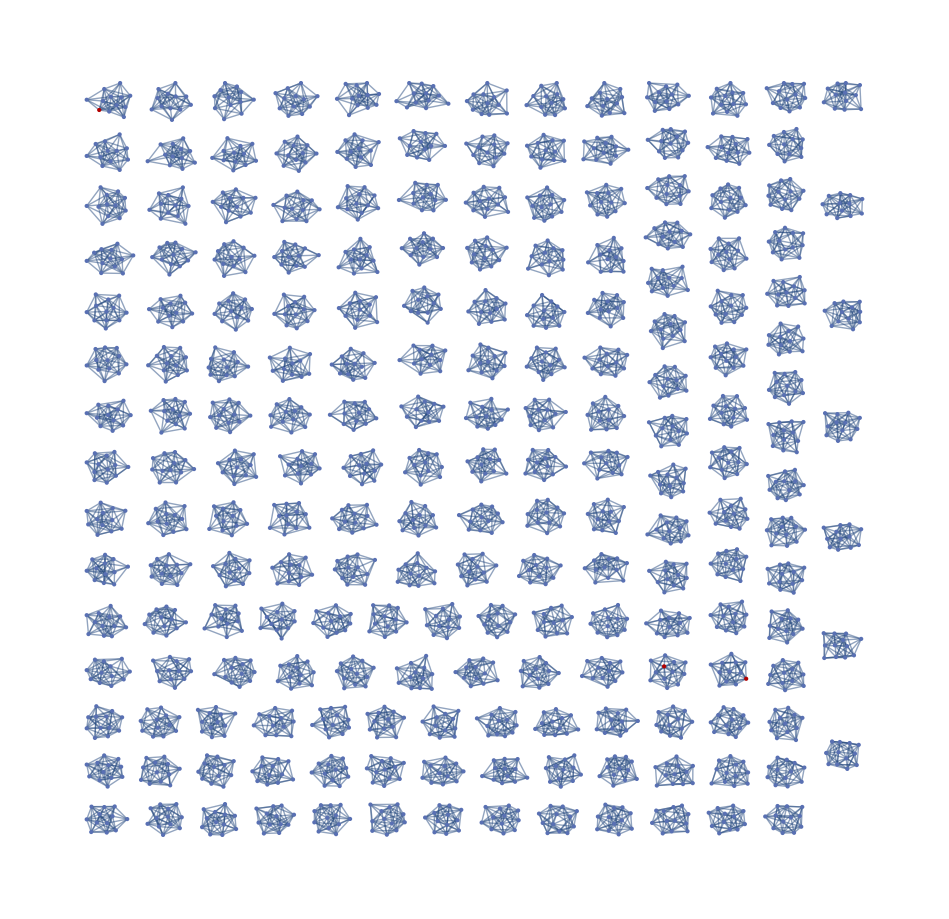

```mathematica
HighlightGraph[g,Keys@Select[agentStates,MatchQ[{"I",_}]]]
```

```mathematica
meetings=DeleteDuplicatesBy[Flatten[Function[a,
{a,#}&/@RandomSample[neighbors[a],Clip[Round[RandomVariate[meetingCounts[a]]],{0,Length[neighbors[a]]}]]]/@Keys[neighbors],1],Sort]
```

{{1,5},{10,1},{11,1},{11,0},{16,15},{16,13},{21,20},{24,35},{30,35},{31,35},{29,28},{35,33},{37,36},{43,45},{43,39},{48,50},{51,55},{52,51},{57,56},{62,66},{63,61},{64,62},{70,69},{72,76},{75,74},{77,78},{77,79},{78,76},{79,74},{84,86},{84,88},{89,87},{91,90},{92,94},{96,98},{102,98},{103,104},{109,110},{115,119},{116,114},{126,128},{122,127},{135,143},{140,141},{142,143},{144,145},{146,154},{148,145},{147,146},{147,149},{152,144},{152,147},{163,159},{162,164},{165,164},{166,158},{173,179},{174,172},{174,173},{170,169},{175,179},{179,169},{184,187},{182,184},{185,182},{186,185},{190,181},{196,197},{197,200},{200,196},{207,205},{207,208},{208,212},{219,216},{220,216},{223,227},{225,219},{226,222},{227,224},{229,235},{233,229},{236,238},{239,231},{240,243},{241,245},{247,251},{247,245},{254,263},{256,260},{266,270},{267,266},{277,281},{283,281},{287,282},{286,277},{288,299},{302,300},{304,308},{304,311},{301,308},{306,308},{309,310},{308,303},{314,319},{316,317},{318,316},{321,317},{330,335},{332,328},{333,325},{336,347},{336,343},{339,347},{340,338},{341,340},{344,336},{345,344},{346,343},{352,349},{352,350},{350,349},{356,355},{361,360},{364,363},{364,366},{364,365},{363,367},{371,370},{370,368},{373,383},{375,380},{375,372},{378,380},{381,382},{382,372},{382,376},{384,386},{391,392},{392,394},{395,387},{401,402},{398,399},{405,407},{406,403},{410,408},{411,409},{412,409},{412,413},{415,418},{409,413},{413,414},{416,415},{421,424},{424,426},{426,427},{430,429},{431,420},{432,435},{433,442},{433,437},{434,437},{436,435},{436,437},{439,435},{441,432},{442,432},{444,454},{445,449},{447,449},{446,448},{453,450},{455,444},{455,450},{456,460},{457,464},{459,457},{460,461},{462,460},{466,465},{468,479},{471,474},{472,475},{473,472},{478,479},{476,473},{477,473},{480,482},{482,483},{484,485},{484,486},{481,490},{485,488},{491,483},{490,489},{493,494},{494,496},{499,501},{502,498},{503,502},{506,505},{508,515},{505,508},{511,515},{512,510},{516,526},{517,518},{520,526},{523,520},{522,518},{519,523},{524,519},{525,516},{527,526},{529,534},{532,537},{536,535},{537,536},{539,537},{540,541},{542,547},{552,553},{563,553},{563,559},{565,569},{566,571},{570,571},{569,568},{580,584},{582,584},{582,585},{582,576},{583,586},{579,583},{586,584},{588,596},{592,590},{591,596},{596,597},{597,593},{604,602},{606,605},{607,609},{610,606},{612,622},{615,613},{624,634},{624,630},{626,628},{626,631},{629,628},{637,647},{641,647},{643,645},{644,641},{644,647},{648,657},{649,658},{651,652},{652,649},{653,658},{650,654},{658,659},{659,655},{667,663},{668,671},{670,666},{671,670},{672,683},{672,675},{673,682},{676,682},{679,680},{680,676},{678,679},{688,685},{688,687},{690,691},{689,692},{694,691},{695,693},{697,705},{697,701},{699,703},{701,696},{704,696},{706,704},{709,715},{714,716},{715,719},{715,716},{727,729},{731,729},{733,732},{734,733},{740,738},{742,734},{744,747},{750,752},{749,755},{758,760},{761,765},{765,767},{767,760},{767,766},{767,758},{766,761},{764,762},{769,778},{772,768},{776,779},{776,775},{778,772},{779,778},{780,790},{784,783},{791,785},{787,783},{789,784},{792,800},{795,797},{796,798},{797,799},{802,799},{805,807},{807,811},{813,812},{819,821},{819,827},{820,821},{823,818},{826,822},{830,828},{834,829},{836,839},{836,835},{833,828},{838,829},{840,841},{844,848},{849,842},{849,841},{849,840},{849,850},{848,845},{850,848},{852,856},{855,863},{856,853},{862,861},{864,873},{864,865},{864,871},{864,867},{865,869},{865,873},{867,868},{867,875},{867,870},{870,873},{871,867},{875,874},{880,876},{880,881},{880,885},{888,889},{890,894},{891,894},{894,895},{893,896},{896,895},{897,896},{901,907},{902,911},{905,909},{906,909},{908,909},{916,913},{917,914},{921,914},{920,915},{923,919},{924,933},{930,929},{927,926},{929,934},{929,926},{932,931},{935,934},{940,941},{941,937},{943,945},{944,940},{947,938},{952,954},{954,950},{956,948},{956,958},{959,955},{961,969},{963,967},{969,960},{964,969},{965,968},{976,975},{977,976},{978,981},{983,978},{985,994},{988,990},{992,995},{994,986},{994,988},{995,988},{996,1000},{999,1003},{1007,999},{1007,997},{1005,1004},{1009,1010},{1011,1008},{1012,1013},{1013,1014},{1018,1016},{1023,1022},{1025,1023},{1027,1030},{1030,1020},{1032,1042},{1038,1036},{1039,1038},{1041,1037},{1041,1033},{1044,1046},{1044,1052},{1045,1049},{1050,1052},{1053,1051},{1054,1053},{1055,1052},{1057,1067},{1058,1062},{1061,1064},{1062,1065},{1066,1062},{1070,1073},{1073,1074},{1071,1078},{1075,1069},{1075,1071},{1074,1072},{1077,1078},{1077,1068},{1086,1084},{1089,1081},{1089,1088},{1091,1081},{1093,1092},{1096,1099},{1098,1101},{1102,1103},{1105,1107},{1108,1105},{1107,1110},{1109,1110},{1115,1111},{1110,1108},{1113,1105},{1114,1113},{1117,1118},{1118,1127},{1123,1118},{1128,1138},{1129,1132},{1133,1139},{1137,1138},{1140,1151},{1142,1146},{1145,1144},{1147,1143},{1148,1140},{1149,1143},{1150,1146},{1151,1143},{1154,1152},{1156,1153},{1160,1162},{1166,1165},{1168,1170},{1169,1166},{1178,1185},{1180,1178},{1179,1178},{1184,1182},{1186,1177},{1187,1177},{1192,1191},{1200,1209},{1208,1204},{1208,1211},{1213,1221},{1219,1221},{1220,1215},{1220,1219},{1224,1225},{1227,1225},{1228,1227},{1231,1235},{1229,1227},{1230,1226},{1234,1230},{1237,1239},{1237,1236},{1240,1242},{1242,1245},{1251,1259},{1249,1250},{1254,1253},{1254,1257},{1257,1248},{1261,1269},{1266,1268},{1268,1271},{1270,1264},{1274,1281},{1276,1280},{1277,1274},{1279,1274},{1280,1278},{1282,1277},{1284,1286},{1288,1293},{1292,1294},{1295,1287},{1295,1291},{1296,1301},{1296,1300},{1298,1306},{1302,1303},{1302,1300},{1297,1302},{1297,1301},{1299,1300},{1305,1306},{1307,1302},{1307,1299},{1308,1318},{1314,1310},{1319,1317},{1320,1331},{1321,1320},{1322,1323},{1322,1321},{1327,1328},{1330,1328},{1336,1333},{1341,1342},{1342,1334},{1346,1348},{1347,1355},{1348,1355},{1350,1346},{1352,1347},{1352,1354},{1355,1344},{1361,1366},{1358,1360},{1362,1366},{1367,1359},{1370,1379},{1371,1376},{1371,1374},{1374,1375},{1374,1373},{1376,1379},{1378,1368},{1381,1383},{1382,1384},{1392,1394},{1395,1398},{1398,1397},{1396,1398},{1396,1393},{1397,1400},{1399,1395},{1399,1398},{1401,1400},{1403,1399},{1407,1405},{1408,1404},{1408,1413},{1418,1422},{1419,1427},{1419,1426},{1420,1416},{1421,1423},{1435,1432},{1445,1440},{1448,1441},{1446,1451},{1447,1445},{1450,1448},{1455,1459},{1456,1452},{1459,1461},{1460,1454},{1467,1464},{1468,1469},{1473,1475},{1475,1467},{1476,1480},{1484,1479},{1485,1482},{1490,1492},{1498,1495},{1502,1507},{1503,1510},{1504,1508},{1510,1506},{1512,1523},{1514,1521},{1516,1520},{1519,1520},{1519,1521},{1523,1522},{1525,1535},{1528,1529},{1529,1527},{1531,1527},{1533,1526},{1539,1541},{1547,1537},{1540,1539},{1548,1554},{1551,1548},{1553,1550},{1558,1559},{1561,1565},{1563,1566},{1564,1565},{1567,1561},{1568,1566},{1571,1567},{1573,1576},{1573,1574},{1575,1572},{1577,1581},{1579,1581},{1582,1577},{1586,1590},{1590,1591},{1592,1588},{1596,1607},{1596,1597},{1600,1603},{1601,1600},{1601,1602},{1602,1597},{1604,1606},{1607,1601},{1610,1612},{1611,1618},{1617,1616},{1617,1608},{1617,1619},{1617,1609},{1618,1619},{1616,1613},{1621,1624},{1621,1630},{1624,1630},{1626,1627},{1628,1623},{1632,1635},{1634,1643},{1639,1638},{1641,1642},{1644,1655},{1644,1654},{1644,1651},{1645,1653},{1649,1652},{1649,1647},{1650,1648},{1651,1654},{1655,1647},{1655,1653},{1656,1664},{1657,1661},{1658,1660},{1667,1657},{1679,1668},{1677,1678},{1674,1671},{1680,1682},{1686,1683},{1686,1688},{1685,1683},{1687,1688},{1692,1702},{1694,1700},{1696,1695},{1697,1692},{1698,1697},{1705,1715},{1706,1711},{1707,1709},{1712,1704},{1712,1707},{1713,1709},{1714,1712},{1714,1711},{1714,1710},{1716,1723},{1721,1726},{1718,1721},{1724,1723},{1724,1716},{1727,1724},{1725,1720},{1725,1726},{1729,1739},{1732,1731},{1736,1733},{1730,1731},{1737,1734},{1738,1728},{1739,1738},{1740,1750},{1744,1742},{1746,1742},{1747,1748},{1749,1750},{1753,1759},{1753,1752},{1754,1761},{1755,1753},{1755,1754},{1758,1754},{1765,1771},{1772,1773},{1775,1766},{1780,1777},{1790,1799},{1796,1795},{1794,1796},{1794,1797},{1797,1798},{1799,1798},{1801,1807},{1808,1809},{1808,1810},{1811,1800},{1814,1822},{1815,1816},{1821,1822},{1825,1833},{1829,1828},{1831,1834},{1835,1831},{1841,1838},{1841,1840},{1845,1838},{1843,1842},{1846,1842},{1848,1851},{1852,1849},{1855,1856},{1850,1854},{1854,1851},{1864,1866},{1865,1868},{1870,1865},{1871,1862},{1877,1880},{1879,1878},{1883,1880},{1884,1886},{1885,1887},{1888,1887},{1893,1891},{1894,1892},{1900,1898},{1901,1897},{1901,1902},{1903,1899},{1905,1906},{1908,1916},{1908,1909},{1912,1914},{1910,1918},{1914,1911},{1915,1918},{1915,1913},{1916,1913},{1917,1913},{1922,1925},{1928,1927},{1934,1942},{1935,1933},{1933,1941},{1938,1939},{1943,1933},{1945,1944},{1945,1955},{1947,1951},{1950,1954},{1952,1951},{1952,1953},{1958,1962},{1960,1967},{1966,1958},{1975,1970},{1975,1978},{1976,1978},{1978,1968},{1978,1969},{1978,1974},{1983,1984},{1984,1988},{1987,1981},{1991,1987},{1995,1992},{1995,2003},{1998,1999},{1994,1996},{1994,1995},{1997,1994},{1999,1992},{2000,1996},{2000,2002},{2003,2000},{2007,2005},{2011,2015},{2016,2019},{2018,2019},{2021,2024},{2023,2025},{2022,2019},{2027,2020},{2028,2032},{2036,2037},{2034,2028},{2034,2029},{2035,2033},{2038,2037},{2038,2029},{2043,2047},{2056,2059},{2055,2057},{2060,2062},{2061,2056},{2062,2061},{2064,2067},{2065,2064},{2071,2072},{2071,2067},{2076,2079},{2077,2079},{2079,2087},{2085,2084},{2089,2091},{2094,2096},{2096,2088},{2100,2103},{2106,2100},{2107,2111},{2109,2110},{2113,2116},{2114,2115},{2116,2120},{2117,2115},{2122,2120},{2123,2121},{2125,2134},{2127,2132},{2129,2133},{2128,2133},{2132,2128},{2135,2133},{2139,2136},{2140,2143},{2143,2145},{2151,2152},{2154,2155},{2155,2157},{2157,2149},{2157,2154},{2157,2159},{2158,2153},{2161,2160},{2164,2163},{2170,2164},{2174,2173},{2180,2176},{2179,2175},{2182,2174},{2184,2188},{2186,2194},{2189,2190},{2195,2184},{2196,2204},{2211,2209},{2212,2209},{2217,2216},{2217,2212},{2218,2209},{2223,2221},{2223,2226},{2231,2225},{2228,2224},{2226,2231},{2227,2226},{2230,2229},{2229,2221},{2232,2239},{2234,2237},{2235,2233},{2238,2237},{2246,2253},{2247,2253},{2248,2250},{2250,2247},{2251,2247},{2251,2250},{2253,2251},{2257,2263},{2259,2261},{2262,2258},{2261,2263},{2264,2260},{2265,2262},{2266,2267},{2266,2258},{2268,2277},{2269,2272},{2271,2276},{2274,2270},{2273,2275},{2277,2275},{2279,2277},{2280,2286},{2281,2290},{2282,2286},{2287,2286},{2287,2288},{2291,2289},{2292,2300},{2293,2302},{2301,2294},{2302,2295},{2306,2304},{2309,2306},{2311,2313},{2311,2315},{2312,2308},{2313,2309},{2314,2305}}

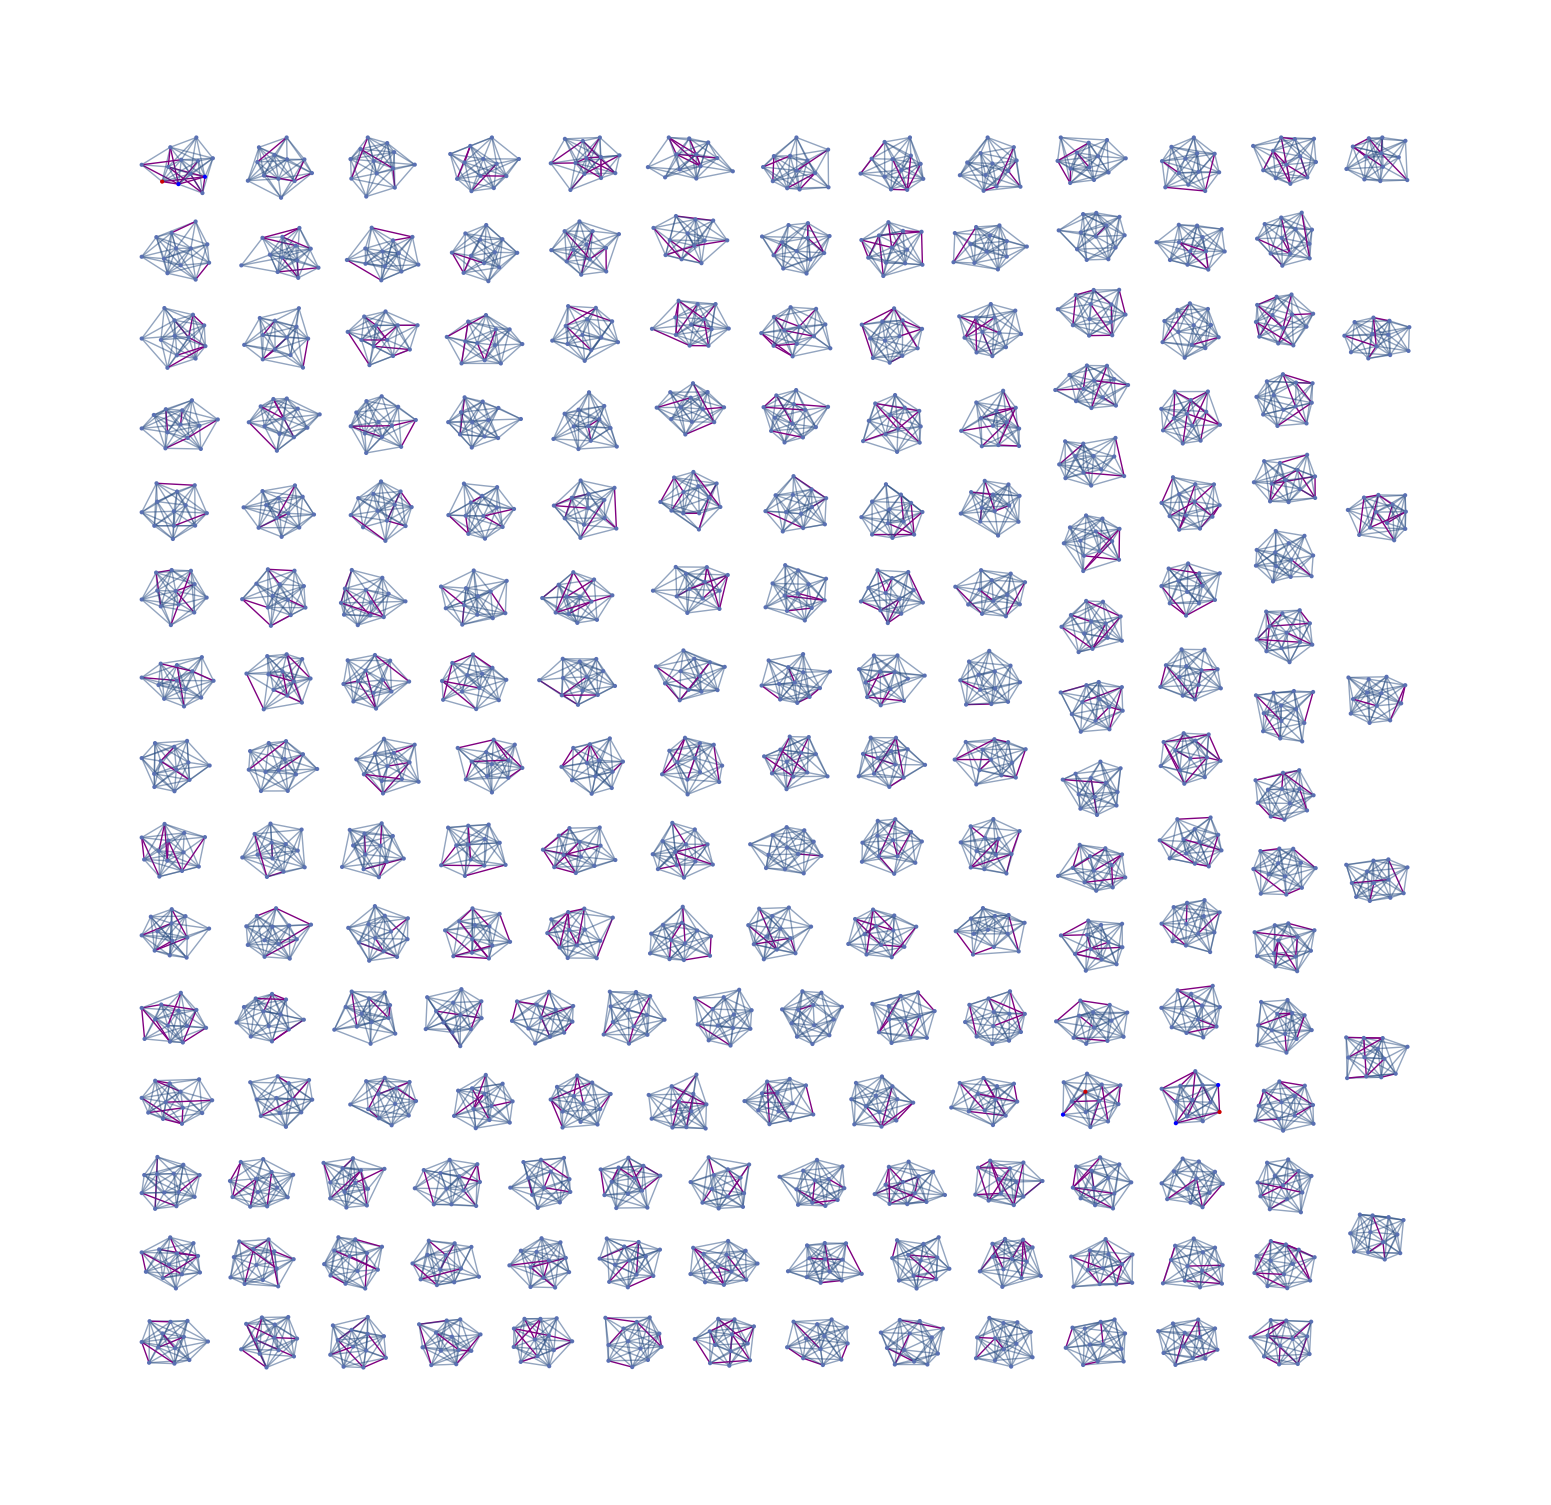

```mathematica
With[{infected=Keys@Select[agentStates,MatchQ[{"I",_}]]},
HighlightGraph[g,{infected,Style[UndirectedEdge@@@meetings,Purple,Thick],
Style[Complement[Flatten[Select[meetings,IntersectingQ[#,infected]&]],infected],Blue]}]]
```

```mathematica
neighbors=agentNeighborhoods[g]
```

<|0→{1,2,3,4,5,8,9,11},1→{0,2,4,5,8,7,10,11},2→{0,1,3,5,6,9,10,11},3→{0,2,4,5,6,7,10,11},4→{0,1,3,5,6,7,8},5→{1,2,3,4,0,6,8,9,7,10},8→{1,4,5,6,7,0,9,10,11},6→{2,3,4,5,7,8,9},9→{2,5,6,7,8,0,10,11},7→{3,4,6,1,5,8,9,10},10→{3,7,8,9,1,2,5,11},11→{8,9,10,0,1,2,3},12→{15,16,18,20,21,22,23},15→{12,13,14,16,17,19,20,23},16→{12,13,14,15,17,19,20},18→{12,14,17,19,20,21,22},13→{15,16,17,20,21,22,23},17→{13,14,15,16,18,19,20,21},14→{15,16,17,18,19,21,22,23},2279,2295→{2294,2292,2296,2297,2300,2301,2302},2298→{2294,2296,2297,2299,2300,2301,2302},2300→{2294,2295,2296,2297,2298,2299,2292,2293,2301,2303},2301→{2294,2297,2298,2299,2300,2293,2295,2302,2303},2302→{2298,2299,2301,2292,2293,2294,2295,2303},2303→{2299,2300,2301,2302,2292,2293,2294,2296},2304→{2305,2306,2308,2310,2312,2313,2314,2315},2305→{2304,2306,2307,2308,2310,2313,2314,2315},2306→{2304,2305,2307,2308,2309,2310,2312,2314,2315},2308→{2304,2305,2306,2307,2309,2310,2311,2312},2310→{2304,2305,2306,2308,2309,2311,2312,2313,2314},2307→{2305,2306,2308,2309,2311,2312,2315},2309→{2306,2307,2308,2310,2311,2312,2313,2315},2311→{2307,2308,2309,2310,2312,2313,2314,2315},2312→{2308,2309,2310,2311,2304,2306,2307,2313,2315},2313→{2309,2310,2311,2312,2304,2305,2314,2315},2315→{2309,2311,2312,2313,2304,2305,2306,2307},2314→{2310,2311,2313,2304,2305,2306}|>
 |  |  |  |

```mathematica
g1 = RandomGraph[WattsStrogatzGraphDistribution[50,0.3,10]]
```

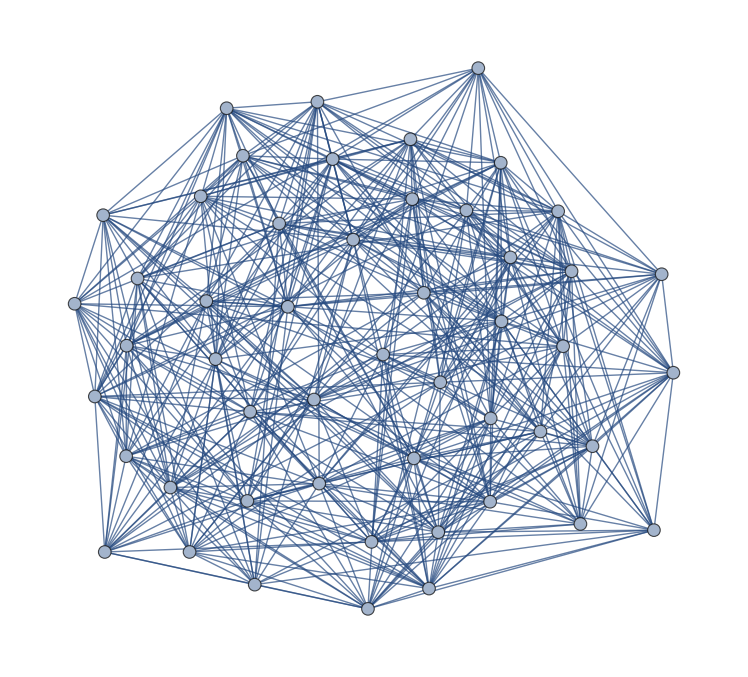
```mathematica
-Graphics-
RandomGraph[WattsStrogatzGraphDistribution[1000,0.1,5]]
```

```mathematica
neighbors1=agentNeighborhoods[g1]
```

<|0→{1,2,3,9,113,13},1→{0,2,3,4,8,9,154,117,157},2→{0,1,3,4,5,9,16,1753,1972,1973},3→{0,1,2,4,5,6,7,8,1754,10,1751},4→{1,2,3,5,6,7,153},5→{2,3,4,6,7,8,9,11,157},6→{3,4,5,7,8,9,111,1165,1975},7→{4,5,6,3,8,739,1162,732},8→{5,6,7,1,3,9,1976,736,738},9→{5,6,8,0,1,2,1167,110,1162,1755},10→{11,14,15,17,18,19,1412,2006,3},11→{10,12,13,14,18,19,5,1168,116},14→{10,11,15,16,17,1417},15→{10,12,14,16,17,18,19,2005,1165,2007},12→{11,15,18,19,1412},13→{11,16,18,17,2006,0,119,1416},16→{13,14,15,17,18,19,1165,2,1165},2137,2154→{2151,2152,2153,2155,2156,2157,1636},2155→{2152,2153,2154,2150,2151,2156,2157,2158,278,1839},2158→{2152,2155,2156,2151,2159,592},2156→{2153,2154,2155,2157,2158,2159,811,1832,813,818},2157→{2154,2155,2156,2150,2153,2159,276,1636,1838,1331},2159→{2156,2157,2158,2150,2152,596,1839},2160→{2161,2162,2163,2166,2167,2168,2169,876},2161→{2160,2162,2163,2164,2166,2168,870,1790,839},2162→{2160,2161,2163,2164,2165,2166,2169,1797,1569,838},2163→{2160,2161,2162,2164,2165,2168,1569,1564},2166→{2160,2162,2164,2161,2167,2168,2169},2164→{2161,2162,2163,2165,2166,2167,318,888,1562,315,311},2165→{2162,2163,2164,2167,2168,830,871},2168→{2163,2165,2166,2160,2161,2169,885,1798},2167→{2164,2165,2166,2160,2169,839,879},2169→{2166,2167,2168,2160,2162,315,883,880,1794}|>
 |  |  |  |

```mathematica
meetingCounts=AssociationThread[Keys[neighbors1], PearsonDistribution[6,0.55216,0.98574,0.000011839,Subscript[b,1],Subscript[b,0]]]
```

<|1→ExponentialDistribution[2],2→ExponentialDistribution[2],31→ExponentialDistribution[2],3→ExponentialDistribution[2],4→ExponentialDistribution[2],5→ExponentialDistribution[2],6→ExponentialDistribution[2],22→ExponentialDistribution[2],7→ExponentialDistribution[2],8→ExponentialDistribution[2],9→ExponentialDistribution[2],10→ExponentialDistribution[2],11→ExponentialDistribution[2],34→ExponentialDistribution[2],12→ExponentialDistribution[2],13→ExponentialDistribution[2],25→ExponentialDistribution[2],14→ExponentialDistribution[2],44→ExponentialDistribution[2],15→ExponentialDistribution[2],16→ExponentialDistribution[2],17→ExponentialDistribution[2],18→ExponentialDistribution[2],19→ExponentialDistribution[2],20→ExponentialDistribution[2],21→ExponentialDistribution[2],23→ExponentialDistribution[2],24→ExponentialDistribution[2],26→ExponentialDistribution[2],27→ExponentialDistribution[2],28→ExponentialDistribution[2],29→ExponentialDistribution[2],30→ExponentialDistribution[2],32→ExponentialDistribution[2],33→ExponentialDistribution[2],35→ExponentialDistribution[2],36→ExponentialDistribution[2],37→ExponentialDistribution[2],38→ExponentialDistribution[2],39→ExponentialDistribution[2],40→ExponentialDistribution[2],41→ExponentialDistribution[2],42→ExponentialDistribution[2],43→ExponentialDistribution[2],45→ExponentialDistribution[2],46→ExponentialDistribution[2],47→ExponentialDistribution[2],48→ExponentialDistribution[2],49→ExponentialDistribution[2],50→ExponentialDistribution[2]|>

```mathematica
recoveryTime=ExponentialDistribution[1/14];
```

```mathematica
PDF[PearsonDistribution[5,Subscript[a,1],Subscript[a,0],Subscript[b,2],Subscript[b,1],Subscript[b,0]],x]
```

```mathematica
agentStates=Join[AssociationThread[Keys[neighbors1],"S"],
AssociationMap[{"I",Floor@RandomVariate[recoveryTime]}&,RandomSample[Keys[neighbors1],3]]]
```

<|1→S,2→{I,4},31→S,3→S,4→S,5→S,6→S,22→S,7→S,8→S,9→S,10→S,11→S,34→S,12→S,13→S,25→S,14→S,44→S,15→S,16→S,17→{I,9},18→S,19→S,20→S,21→S,23→S,24→{I,20},26→S,27→S,28→S,29→S,30→S,32→S,33→S,35→S,36→S,37→S,38→S,39→S,40→S,41→S,42→S,43→S,45→S,46→S,47→S,48→S,49→S,50→S|>

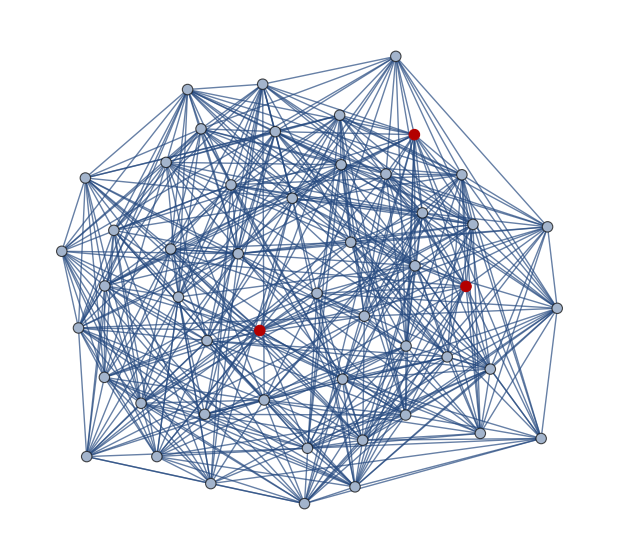

```mathematica
HighlightGraph[g1,Keys@Select[agentStates,MatchQ[{"I",_}]]]
```

```mathematica
meetings=DeleteDuplicatesBy[Flatten[Function[a,{a,#}&/@RandomSample[neighbors1[a],Clip[Round[RandomVariate[meetingCounts[a]]],{0,Length[neighbors1[a]]}]]]/@Keys[neighbors1],1],Sort]
```

{{31,29},{4,6},{6,45},{8,29},{10,15},{13,17},{25,13},{44,46},{17,25},{26,13},{27,36},{28,48},{29,6},{30,29},{32,40},{35,33},{35,44},{38,37},{39,19},{43,50},{43,44},{46,1},{47,1},{49,5},{49,7}}

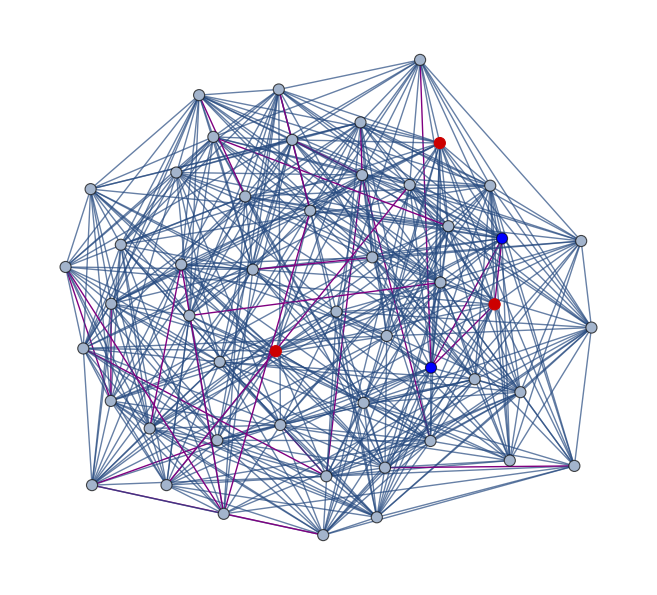

```mathematica
With[{infected=Keys@Select[agentStates,MatchQ[{"I",_}]]},HighlightGraph[g1,{infected, Style[UndirectedEdge@@@meetings,Purple,Thick], Style[Complement[Flatten[Select[meetings,IntersectingQ[#,infected]&]],infected],Blue]}]]
```

```mathematica
simulate[neighbors_,meetingCounts_,recoveryTime_,initialInfected_List,maxSteps_,loggingFunc_] :=
Module[{stateAgents, agentRecoveryTimes, agentMeetings, steps, output},
	agentMeetings[a_] :=
		RandomSample[neighbors[a],UpTo@Ramp@Round@RandomVariate[meetingCounts[a]]];
	agentRecoveryTimes = AssociationMap[RandomVariate[recoveryTime]&,initialInfected];
	stateAgents = <|
			"S"->CreateDataStructure["HashSet",Complement[Keys[neighbors],initialInfected]],
			"I"->CreateDataStructure["HashSet",initialInfected],
			"R"->CreateDataStructure["HashSet"]
		|>;
	output = {loggingFunc[stateAgents]};
	steps = 0;
	While[steps++ < maxSteps && stateAgents["I"]["Length"] > 0,
		Module[{newStateAgents},
			newStateAgents = #["Copy"]&/@stateAgents;
			(*Mark appropriate agents as recovered*)
			KeyValueMap[
				If[#2≤0,
					KeyDropFrom[agentRecoveryTimes,#1];
					newStateAgents["I"]["Remove",#1];
					newStateAgents["R"]["Insert",#1];
				]&,
				agentRecoveryTimes
			];
			(*Make infected agents meet their neighbors*)
			Function[infectedAgent,
				Module[{newInfected},
					newInfected = Select[
							agentMeetings[infectedAgent],
							stateAgents["S"]["MemberQ",#]&
						];
					newStateAgents["S"]["Remove",#]&/@newInfected;
					newStateAgents["I"]["Union",newInfected];
					(agentRecoveryTimes[#] = RandomVariate[recoveryTime])&/@newInfected;
				]
			]/@Normal[stateAgents["I"]];
			(*Make the susceptible neighbors of infected agents meet their neighbors*)
			Function[neighborOfInfected,
				Module[{metInfected},
					If[stateAgents["S"]["MemberQ",neighborOfInfected],
						metInfected = AnyTrue[
								agentMeetings[neighborOfInfected],
								stateAgents["I"]["MemberQ",#]&
							];
						If[metInfected,
							newStateAgents["S"]["Remove",neighborOfInfected];
							newStateAgents["I"]["Insert",neighborOfInfected];
							agentRecoveryTimes[neighborOfInfected] = RandomVariate[recoveryTime];The probability density ￼ satisfies the differential equation
						]
					]
				]
			]/@Flatten[Lookup[neighbors,Normal[stateAgents["I"]]],1];
			(*Decrement the recovery times*)
			agentRecoveryTimes -= 1;
			stateAgents = newStateAgents;
		];
		AppendTo[output, loggingFunc[stateAgents]];
	];
	output
]

simulate[neighbors_,meetingCounts_,recoveryTime_,initialInfectedCount_Integer,maxSteps_,loggingFunc_] :=
	simulate[neighbors,meetingCounts,recoveryTime,
		RandomSample[Keys[neighbors], initialInfectedCount],
		maxSteps,loggingFunc]

simulate[neighbors_, meetingCounts_, recoveryTime_, initialInfectedSpec_, maxSteps_] :=
	simulate[neighbors,meetingCounts,recoveryTime,initialInfectedSpec,maxSteps,
		Function[stateAgents,#["Length"]&/@Lookup[stateAgents,{"I","S","R"}]]
	]
```

```mathematica
sim=simulate[agentNeighborhoods[g1],AssociationMap[GammaDistribution[1/0.4,0.3]&,VertexList[g1]],GammaDistribution[1/7, 0.3],10,Infinity];
```

```mathematica
peakInfected[sim_]:=Max[SIM[[All,1]]]/Total[sim[[1]]]
```

```mathematica
totalInfected[sim_]:=(sim[[-1,1]]+sim[[-1,3]])/Total[sim[[-1]]]
```

```mathematica
sims=Association@Table[m->simulate[sims=Association@Table[m->simulate[agentNeighborhoods[g1],
AssociationMap[ExponentialDistribution[1/m]&,VertexList[g1]],
GeometricDistribution[1/(1+7)],10,Infinity],{m,0.05,1,0.01}];agentNeighborhoods[g1],AssociationMap[ExponentialDistribution[1/m]&,VertexList[g1]],GeometricDistribution[1/(1+7)],10,Infinity],{m,0.05,1,0.01}];
```

```mathematica
sirPlot[sim_,opts___]:=StackedListPlot[Transpose[sim],Frame->{{True,False},{True,False}},FrameLabel->{"step","agents"},opts]
```

```mathematica
ListAnimate[KeyValueMap[sirPlot[#2,PlotLabel->#1]&,sims],AnimationRunning->False]
```

```mathematica
ListLinePlot[{KeyValueMap[List,peakInfected/@sims],KeyValueMap[List,totalInfected/@sims]},]
```

## Measure Interactions

```mathematica
g1=generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],217],WattsStrogatzGraphDistribution[10,0.2, 3],4]
```

-Graphics-

```mathematica
neighbors=agentNeighborhoods[g1]
```

<|0→{2,3,4,6,7,8,9,1615,1773,1777},2→{0,1,3,5,6,8,9,1773,138,142,2083},3→{0,1,2,4,5,6,1113,1619},4→{0,3,6,7,8,2080,1572},6→{0,3,4,5,2,7,8,144,1576,137,1114,1577,1579,2080},1→{2,3,5,9},5→{1,2,3,6,7,8,136,1117,1777,134,140,1616},7→{4,5,6,0,8,9,1618},8→{5,6,7,0,2,4,9,2088,1116},9→{7,8,0,1,2,142},10→{11,12,13,15,17,18,19,1727},11→{10,12,13,14,18,387,384},12→{10,11,13,14,16,19,973,387,690,1060,1727},13→{10,11,12,14,15,16,19,972,977},15→{10,13,14,16,17,18,1062,1722},14→{11,12,13,15,16,17,411,697,695,1069},16→{13,14,15,12,18,19,388,410},2137,2155→{2150,2153,2154,2156,2158,1021,1883},2157→{2151,2152,2154,2156,2150,2158,2159,229,1026,1889,2054,315,1027},2154→{2152,2153,2155,2157,2159,224,315,313},2156→{2153,2155,2157,2158,2159,1775},2159→{2154,2156,2157,2158,2150,2151,2152,1779,1779},2158→{2155,2156,2157,2150,2151,2159,2054},2160→{2161,2162,2163,2167,2168,2169,360,1360},2161→{2160,2162,2163,2164,2168,2169,362,921,2041,532,926},2162→{2160,2161,2163,2164,2165,2166,533,362,535},2163→{2160,2161,2162,2164,2165,2168,361,2047},2164→{2161,2162,2163,2165,2166,2167,1361},2165→{2162,2163,2164,2166,2167,2169,922,1368,1362,1979},2168→{2163,2166,2167,2160,2161,2169,1975,2041,925},2166→{2164,2165,2162,2167,2168,2169,2048},2167→{2164,2165,2166,2160,2168,2169,1973},2169→{2165,2166,2167,2168,2160,2161,535,1977}|>
 |  |  |  |

```mathematica
meetingCounts1=AssociationThread[Keys[neighbors], PearsonDistribution[6, 0.55216,0.98574,0.000011839,0.1,0.1]]
```

<|0→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],2→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],3→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],4→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],6→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],1→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],5→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],7→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],8→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],9→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],2151,2161→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],2162→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],2163→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],2164→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],2165→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],2168→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],2166→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],2167→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1],2169→PearsonDistribution[6,0.55216,0.98574,0.000011839,0.1,0.1]|>
 |  |  |  |

```mathematica
recoveryTime1=ExponentialDistribution[1/14];
```

```mathematica
agentStates1=Join[AssociationThread[Keys[neighbors],"S"],
AssociationMap[{"I",Floor@RandomVariate[recoveryTime1]}&,RandomSample[Keys[neighbors],3]]]
```

<|0→S,2→S,3→S,4→S,6→S,1→S,5→S,7→S,8→S,9→S,10→S,11→S,12→S,13→S,15→S,14→S,16→S,17→S,18→S,19→S,20→S,21→S,23→S,24→S,22→S,26→S,25→S,27→S,28→S,29→S,30→S,31→S,32→S,33→S,34→S,35→S,37→S,36→S,38→S,39→S,40→S,41→S,42→S,43→S,44→S,45→S,47→S,46→S,48→S,49→S,50→S,51→S,53→S,55→S,52→S,54→S,56→S,57→S,58→S,59→S,60→S,61→S,62→S,63→S,65→S,64→S,67→S,66→S,68→S,69→S,70→S,71→S,72→S,73→S,74→S,75→S,78→S,79→S,76→S,77→S,80→S,82→S,83→S,85→S,81→S,84→S,87→S,86→S,88→S,89→S,90→S,91→S,92→S,93→S,94→S,95→S,96→S,98→S,97→S,99→S,100→S,101→S,103→S,102→S,104→S,105→S,106→S,107→S,109→S,108→S,110→S,112→S,113→S,114→S,111→S,116→S,115→S,117→S,118→S,119→S,120→S,121→S,122→S,123→S,124→S,127→S,125→S,126→S,128→S,129→S,130→S,131→S,132→S,134→S,133→S,135→S,138→S,136→S,139→S,137→S,140→S,141→S,142→S,143→S,144→S,145→S,146→S,148→S,149→S,147→S,150→S,151→S,153→S,152→S,157→S,154→S,158→S,155→S,156→S,159→S,160→S,162→S,163→S,161→S,164→S,166→S,169→S,165→S,167→S,168→S,170→S,171→S,173→S,174→S,172→S,177→S,175→S,176→S,178→S,179→S,180→S,181→S,182→S,185→S,183→S,184→S,186→S,188→S,187→S,189→S,190→S,192→S,193→S,191→S,197→S,194→S,195→S,196→S,198→S,199→S,200→S,201→S,202→S,203→S,204→S,205→S,206→S,207→S,208→S,209→S,210→S,211→S,212→S,213→S,214→S,215→S,216→S,217→S,218→S,219→S,220→S,221→S,222→S,223→S,224→S,227→S,225→S,226→S,228→S,229→S,230→S,231→S,232→S,233→S,234→S,236→S,235→S,237→S,238→S,239→S,240→S,242→S,243→S,241→S,245→S,244→S,246→S,247→S,248→S,249→S,250→S,251→S,252→S,253→S,256→S,254→S,255→S,258→S,259→S,257→S,260→S,261→S,262→S,263→S,265→S,264→S,266→S,267→S,268→S,269→S,270→S,272→S,273→S,271→S,274→S,275→S,277→S,276→S,278→S,279→S,280→S,282→S,286→S,281→S,283→S,284→S,285→S,288→S,287→S,289→S,290→S,291→S,293→S,292→S,294→S,295→S,296→S,297→S,298→S,299→S,300→S,303→S,304→S,301→S,302→S,305→S,307→S,306→S,308→S,309→S,310→S,311→S,312→S,313→S,314→S,317→S,315→S,316→S,319→S,318→S,320→S,321→S,322→S,323→S,324→S,326→S,325→S,327→S,328→S,329→S,330→S,331→S,332→S,333→S,334→S,336→S,335→S,337→S,339→S,338→S,340→S,341→S,342→S,343→S,344→S,345→S,346→S,347→S,348→S,349→S,350→S,351→S,352→S,353→S,354→S,355→S,356→S,359→S,357→S,358→S,360→S,361→S,362→S,363→S,367→S,364→S,366→S,365→S,368→S,369→S,370→S,371→S,372→S,373→S,374→S,375→S,376→S,377→S,378→S,379→S,380→S,381→S,382→S,383→S,384→S,385→S,386→S,387→S,388→S,389→S,390→S,391→S,393→S,394→S,395→S,392→S,396→S,397→{I,5},398→S,399→S,400→S,401→S,402→S,405→S,408→S,403→S,404→S,407→S,406→S,409→S,410→S,411→S,412→S,413→S,414→S,416→S,415→S,418→S,417→S,419→S,420→S,421→S,422→S,423→S,425→S,424→S,426→S,428→S,427→S,429→S,430→S,431→S,432→S,433→S,434→S,435→S,439→S,436→S,437→S,438→S,440→S,442→S,443→S,446→S,441→S,444→S,447→S,445→S,448→S,449→S,450→S,451→S,452→S,453→S,454→S,457→S,455→S,456→S,458→S,459→S,460→S,462→S,463→S,464→S,466→S,461→S,465→S,467→S,469→S,468→S,470→S,471→S,472→S,473→S,474→S,475→S,476→S,478→S,477→S,479→S,480→S,481→S,482→S,483→S,484→S,487→S,485→S,486→S,488→S,489→S,490→S,491→S,492→S,493→S,494→S,495→S,499→S,496→S,497→S,498→S,500→S,501→S,502→S,503→S,504→S,505→S,508→S,506→S,507→S,509→S,510→S,512→S,513→S,511→S,514→S,516→S,515→S,517→S,519→S,518→S,520→S,521→S,522→S,523→S,524→S,525→S,526→S,527→S,528→S,529→S,530→S,531→S,532→S,533→S,535→S,536→S,534→S,537→S,539→S,538→S,540→S,541→S,542→S,543→S,544→S,546→S,547→S,545→S,548→S,549→S,550→S,551→S,552→S,553→S,554→S,555→S,557→S,556→S,558→S,559→S,560→S,561→S,562→S,563→S,564→S,565→S,566→S,567→S,568→S,569→S,570→S,571→S,572→S,573→S,574→S,575→S,579→S,576→S,577→S,578→S,580→S,581→S,582→S,584→S,586→S,583→S,587→S,585→S,589→S,588→S,590→S,591→S,592→S,593→S,594→S,595→S,597→S,596→S,599→S,598→S,600→S,601→S,602→S,603→S,604→S,605→S,606→S,609→S,607→S,608→S,610→S,611→S,612→S,613→S,614→S,615→S,617→S,619→S,616→S,618→S,620→S,621→S,622→S,623→S,624→S,626→S,627→S,625→S,628→S,629→S,630→S,631→S,632→S,633→S,634→S,635→S,636→S,637→S,638→S,639→S,640→S,641→S,642→S,643→S,644→S,647→S,649→S,645→S,648→S,646→S,650→S,651→S,652→S,653→S,654→S,655→S,656→S,657→S,658→S,659→S,660→S,661→S,662→S,663→S,664→S,665→S,666→S,667→S,668→S,669→S,670→S,671→S,672→S,673→S,674→S,675→S,677→S,676→S,678→S,679→S,680→S,681→S,683→S,682→S,684→S,685→S,686→S,687→S,688→S,689→S,690→S,692→S,693→S,694→S,691→S,695→S,698→S,696→S,697→S,699→S,700→S,701→S,702→S,704→S,703→S,705→S,707→S,709→S,706→S,708→S,710→S,711→S,712→S,713→S,715→S,716→S,714→S,717→S,718→S,719→S,720→S,721→S,722→S,723→S,729→S,726→S,724→S,725→S,727→S,728→S,730→S,731→S,732→S,733→S,735→S,734→S,736→S,739→S,738→S,737→S,740→S,741→S,742→S,743→S,744→S,745→S,746→S,748→S,747→S,749→S,750→S,751→S,752→S,753→S,754→S,755→S,756→S,757→S,758→S,759→S,760→S,761→S,762→S,763→S,765→S,767→S,764→S,766→S,768→S,769→S,770→S,771→S,772→S,773→S,774→S,776→S,775→S,777→S,778→S,779→S,780→S,781→S,782→S,783→S,784→S,787→S,786→S,788→S,785→S,789→S,790→S,791→S,792→S,793→S,794→S,795→S,796→S,797→S,798→S,799→S,800→S,801→S,802→S,803→S,804→S,805→S,808→S,806→S,807→S,809→S,810→S,812→S,813→S,811→S,814→S,815→S,818→S,819→S,816→S,817→S,820→S,821→S,823→S,824→S,825→S,822→S,828→S,826→S,827→S,829→S,830→S,831→S,833→S,832→S,834→S,835→S,836→S,837→S,838→S,839→S,840→S,841→S,842→S,843→S,844→S,846→S,845→S,847→S,848→S,849→S,850→S,851→S,853→S,852→S,854→S,855→S,856→S,858→S,857→S,859→S,860→S,861→S,862→S,863→S,865→S,866→S,864→S,867→S,868→S,869→S,870→S,871→S,872→S,873→S,879→S,874→S,875→S,876→S,877→S,878→S,880→S,881→S,882→S,883→S,885→S,887→S,884→S,886→S,888→S,889→S,890→S,891→S,892→S,893→S,894→S,896→S,895→S,897→S,898→S,899→S,900→S,901→S,902→S,903→S,904→S,905→S,906→S,907→S,908→S,909→S,910→S,912→S,913→S,911→S,914→S,915→S,916→S,917→S,918→S,919→S,920→S,922→S,923→S,926→S,921→S,924→S,925→S,927→S,929→S,928→S,930→S,931→S,932→S,933→S,934→S,935→S,936→S,938→S,937→S,939→S,940→S,942→S,943→S,946→S,941→S,944→S,945→S,947→S,948→S,949→S,950→S,951→S,952→S,953→S,956→S,954→S,955→S,957→S,958→S,959→S,960→S,961→S,962→S,963→S,966→S,968→S,964→S,965→S,967→S,969→S,970→S,971→S,972→S,973→S,974→S,975→S,976→S,977→S,979→S,978→S,980→S,981→S,982→S,983→S,984→S,985→S,986→S,988→S,987→S,989→S,990→S,991→S,992→S,993→S,994→S,995→S,996→S,997→S,998→S,999→S,1000→S,1001→S,1002→S,1003→S,1004→S,1005→S,1006→S,1007→S,1009→S,1008→S,1010→S,1011→S,1012→S,1014→S,1013→S,1015→S,1016→S,1017→S,1018→S,1019→S,1020→S,1021→S,1022→S,1023→S,1024→S,1025→S,1026→S,1027→S,1028→S,1029→S,1030→S,1031→S,1032→S,1033→S,1034→S,1035→S,1036→S,1039→S,1037→S,1038→S,1040→S,1041→S,1042→S,1043→S,1044→S,1045→S,1046→S,1047→S,1048→S,1049→S,1050→S,1051→S,1052→S,1053→S,1054→S,1055→S,1056→S,1057→S,1059→S,1058→S,1060→S,1061→S,1062→S,1063→S,1064→S,1065→S,1067→S,1066→S,1068→S,1069→S,1070→S,1071→S,1072→S,1073→S,1074→S,1075→S,1076→S,1078→S,1077→S,1079→S,1080→S,1081→S,1082→S,1083→S,1086→S,1084→S,1085→S,1087→S,1088→S,1089→S,1090→S,1091→S,1092→S,1093→S,1094→S,1095→S,1096→S,1097→S,1098→S,1099→S,1100→S,1101→S,1103→S,1105→S,1106→S,1102→S,1107→S,1104→S,1108→S,1109→S,1110→S,1111→S,1112→S,1113→S,1114→S,1115→S,1116→S,1117→S,1119→S,1118→S,1120→S,1121→S,1122→S,1123→S,1124→S,1125→S,1126→S,1129→S,1127→S,1128→S,1130→S,1131→S,1132→S,1133→S,1135→S,1134→S,1136→S,1139→S,1137→S,1138→S,1140→S,1141→S,1142→S,1143→S,1144→S,1146→S,1145→S,1147→S,1148→S,1149→S,1150→S,1151→S,1153→S,1152→S,1154→S,1155→S,1156→S,1159→S,1157→S,1158→S,1160→S,1161→S,1162→S,1163→S,1164→S,1167→S,1165→S,1166→S,1169→S,1168→S,1170→S,1171→S,1172→S,1173→S,1174→S,1175→S,1176→S,1177→S,1179→S,1178→S,1180→S,1181→S,1182→S,1183→S,1185→S,1184→S,1186→S,1188→S,1187→S,1189→S,1190→S,1192→S,1194→S,1196→S,1191→S,1193→S,1195→S,1197→S,1198→S,1199→S,1200→S,1201→S,1202→S,1203→S,1204→S,1205→S,1206→S,1207→S,1209→S,1208→S,1210→S,1212→S,1216→S,1211→S,1213→S,1214→S,1218→S,1215→S,1217→S,1219→S,1220→S,1221→S,1222→S,1224→S,1225→S,1223→S,1228→S,1226→S,1227→S,1229→S,1230→S,1231→S,1232→S,1233→S,1234→S,1235→S,1236→S,1237→S,1238→S,1239→S,1240→S,1241→S,1242→S,1244→S,1243→S,1245→S,1246→S,1248→S,1247→S,1249→S,1250→S,1251→S,1252→S,1253→S,1254→S,1255→S,1258→S,1256→S,1257→S,1259→S,1260→S,1261→S,1263→S,1266→S,1264→S,1262→S,1265→S,1267→S,1268→S,1269→S,1270→S,1271→S,1272→S,1273→S,1274→S,1275→S,1276→S,1277→S,1278→S,1279→S,1280→S,1281→S,1282→S,1283→S,1285→S,1284→S,1289→S,1287→S,1286→S,1288→S,1290→S,1291→S,1292→S,1295→S,1293→S,1294→S,1297→S,1296→S,1298→S,1299→S,1300→S,1302→S,1303→S,1306→S,1301→S,1304→S,1305→S,1309→S,1307→S,1308→S,1310→S,1311→S,1312→S,1313→S,1314→S,1315→S,1316→S,1317→S,1318→S,1319→S,1320→S,1321→S,1322→S,1323→S,1325→S,1324→S,1326→S,1327→S,1328→S,1329→S,1330→S,1331→S,1332→S,1333→S,1334→S,1335→S,1337→S,1336→S,1338→S,1339→S,1340→S,1341→S,1342→S,1343→S,1344→S,1345→S,1347→S,1346→S,1348→S,1349→S,1350→S,1351→S,1352→S,1353→S,1356→S,1354→S,1355→S,1357→S,1358→S,1359→S,1360→S,1361→S,1362→S,1363→S,1367→S,1364→S,1365→S,1366→S,1369→S,1368→S,1370→S,1371→S,1372→S,1373→S,1375→S,1374→S,1376→S,1378→S,1377→S,1379→S,1380→S,1382→S,1384→S,1386→S,1381→S,1383→S,1385→S,1387→S,1388→S,1389→S,1390→S,1391→S,1393→S,1394→S,1396→S,1392→S,1395→S,1397→S,1398→S,1399→S,1400→S,1401→S,1402→S,1403→S,1404→S,1405→S,1407→S,1406→S,1408→S,1409→S,1410→S,1411→S,1413→S,1412→S,1414→S,1415→S,1416→S,1417→S,1418→S,1419→S,1420→S,1422→S,1424→S,1421→S,1423→S,1426→S,1425→S,1427→S,1428→S,1429→S,1430→S,1431→S,1432→S,1433→S,1434→S,1435→S,1437→S,1436→S,1438→S,1439→S,1440→S,1441→S,1442→S,1443→S,1444→S,1445→S,1448→S,1446→S,1447→S,1449→S,1450→S,1451→S,1452→S,1453→S,1454→S,1455→S,1456→S,1457→S,1458→S,1459→S,1460→S,1461→S,1462→S,1463→S,1464→S,1466→S,1465→S,1467→S,1468→S,1469→S,1470→S,1471→S,1472→S,1473→S,1475→S,1474→S,1477→S,1476→S,1478→S,1479→S,1480→S,1481→S,1482→S,1483→S,1485→S,1484→S,1486→S,1488→S,1487→S,1489→S,1490→S,1491→S,1492→S,1493→S,1494→S,1495→S,1496→S,1497→S,1498→S,1499→S,1500→S,1502→S,1503→S,1501→S,1504→S,1505→S,1508→S,1506→S,1509→S,1507→S,1510→S,1511→S,1512→S,1513→S,1514→S,1516→S,1515→S,1517→S,1518→S,1519→S,1520→S,1522→S,1521→S,1523→S,1526→S,1524→S,1525→S,1527→S,1528→S,1529→S,1530→S,1531→S,1532→S,1534→S,1533→S,1537→S,1538→S,1535→S,1536→S,1539→S,1540→S,1541→S,1543→S,1542→S,1544→S,1545→S,1546→S,1547→S,1548→S,1549→S,1550→S,1551→S,1552→S,1553→S,1556→S,1554→S,1555→S,1558→S,1557→S,1559→S,1560→S,1561→S,1562→S,1565→S,1563→S,1564→S,1566→S,1567→S,1568→S,1569→S,1570→S,1571→S,1572→S,1573→S,1574→S,1575→S,1576→S,1578→S,1577→S,1579→S,1580→S,1581→S,1582→S,1584→S,1583→S,1585→S,1586→S,1587→S,1588→S,1589→S,1590→S,1591→S,1593→S,1592→S,1594→S,1595→S,1596→S,1599→S,1597→S,1598→S,1600→S,1601→S,1602→S,1603→S,1604→S,1605→S,1606→S,1607→S,1608→S,1609→S,1610→S,1611→S,1612→S,1613→S,1614→S,1615→S,1616→S,1617→S,1618→S,1619→S,1620→S,1621→S,1622→S,1623→S,1624→S,1625→S,1626→S,1627→S,1628→S,1629→S,1630→S,1631→S,1632→S,1633→S,1634→S,1635→S,1636→S,1637→S,1638→S,1639→S,1640→S,1641→S,1643→S,1642→S,1644→S,1645→S,1646→S,1647→S,1648→S,1649→S,1650→S,1652→S,1653→S,1654→S,1651→S,1655→S,1656→S,1657→S,1658→S,1659→S,1660→S,1661→S,1662→S,1663→S,1664→S,1666→S,1665→S,1667→S,1668→S,1669→S,1670→S,1671→S,1672→S,1673→S,1674→S,1675→S,1676→S,1677→S,1678→S,1679→S,1680→S,1682→S,1683→S,1681→S,1684→S,1685→S,1686→S,1687→S,1689→S,1688→S,1690→S,1692→S,1693→S,1691→S,1694→S,1695→S,1696→S,1697→S,1698→S,1699→S,1700→S,1701→S,1702→S,1703→S,1704→S,1705→S,1706→S,1707→S,1709→S,1708→S,1710→S,1711→S,1712→S,1713→S,1714→S,1715→S,1716→S,1717→S,1718→S,1719→S,1720→S,1723→S,1724→S,1726→S,1721→S,1722→S,1725→S,1727→S,1728→S,1729→S,1730→S,1731→S,1732→S,1733→S,1734→S,1735→S,1738→S,1736→S,1739→S,1737→S,1740→S,1741→S,1742→S,1743→S,1744→S,1745→S,1746→S,1747→S,1748→S,1749→S,1750→S,1751→S,1752→S,1753→S,1754→S,1755→S,1756→S,1757→S,1758→S,1759→S,1760→S,1761→S,1763→S,1766→S,1762→S,1764→S,1765→S,1767→S,1768→S,1769→S,1770→S,1771→S,1772→S,1773→S,1774→S,1777→S,1775→S,1776→S,1778→S,1779→S,1780→S,1781→S,1782→S,1784→S,1783→S,1785→S,1786→S,1787→S,1789→S,1788→S,1790→S,1791→S,1793→S,1796→S,1792→S,1794→S,1795→S,1797→S,1798→S,1799→S,1800→S,1802→S,1803→S,1806→S,1801→S,1804→S,1807→S,1805→S,1808→S,1809→S,1810→S,1811→S,1812→S,1813→S,1815→S,1814→S,1816→S,1817→S,1819→S,1818→S,1820→S,1821→S,1822→S,1823→S,1824→S,1825→S,1826→S,1827→S,1828→S,1829→S,1830→S,1831→S,1833→S,1832→S,1834→S,1835→S,1836→S,1838→S,1837→S,1839→S,1840→S,1841→S,1842→S,1843→S,1846→S,1844→S,1845→S,1847→S,1848→S,1849→S,1850→S,1851→S,1852→S,1853→S,1854→S,1855→S,1856→S,1857→S,1858→S,1859→S,1860→S,1861→S,1862→S,1863→S,1864→S,1865→S,1866→S,1867→S,1868→S,1869→S,1870→S,1871→S,1872→S,1873→S,1874→S,1875→S,1876→S,1877→S,1878→S,1879→S,1880→S,1881→S,1882→S,1883→S,1884→S,1885→S,1887→S,1886→S,1888→S,1889→S,1890→S,1891→S,1892→S,1893→S,1894→S,1896→{I,6},1895→S,1897→S,1898→S,1899→S,1900→S,1901→S,1902→S,1903→S,1906→S,1904→S,1907→S,1905→S,1908→S,1909→S,1910→S,1911→S,1913→S,1914→S,1915→S,1917→S,1912→S,1916→S,1918→S,1919→S,1920→S,1921→S,1923→S,1924→S,1925→S,1922→S,1926→S,1927→S,1928→S,1929→S,1930→S,1931→S,1933→S,1932→S,1934→S,1936→S,1935→S,1937→S,1938→S,1939→S,1940→S,1941→S,1942→S,1943→S,1944→S,1945→S,1946→S,1949→S,1947→S,1948→S,1950→S,1951→S,1952→S,1953→S,1954→S,1955→S,1956→S,1957→S,1958→S,1959→S,1960→S,1963→S,1961→S,1964→S,1962→S,1965→S,1966→S,1968→S,1969→S,1967→S,1970→S,1971→S,1972→S,1975→S,1973→S,1974→S,1976→S,1977→S,1978→S,1979→S,1980→S,1981→S,1983→S,1986→S,1982→S,1984→S,1985→S,1987→S,1989→S,1988→S,1990→S,1992→S,1993→S,1991→S,1994→S,1995→S,1996→S,1999→S,1997→S,1998→S,2000→S,2001→S,2002→S,2003→S,2004→S,2005→S,2006→S,2007→S,2008→S,2009→S,2010→S,2011→S,2012→S,2013→S,2014→S,2016→S,2015→S,2017→S,2018→S,2019→S,2020→S,2021→S,2022→S,2023→S,2024→S,2025→S,2026→S,2027→S,2028→S,2029→S,2030→S,2032→S,2031→S,2033→S,2034→S,2035→S,2036→{I,11},2037→S,2039→S,2038→S,2040→S,2041→S,2043→S,2046→S,2042→S,2044→S,2045→S,2047→S,2048→S,2049→S,2050→S,2051→S,2052→S,2053→S,2054→S,2055→S,2056→S,2057→S,2058→S,2059→S,2060→S,2062→S,2063→S,2061→S,2064→S,2065→S,2068→S,2066→S,2067→S,2069→S,2070→S,2071→S,2072→S,2074→S,2073→S,2076→S,2075→S,2077→S,2078→S,2079→S,2080→S,2082→S,2083→S,2081→S,2084→S,2085→S,2086→S,2087→S,2088→S,2089→S,2090→S,2091→S,2092→S,2093→S,2094→S,2095→S,2098→S,2096→S,2097→S,2099→S,2100→S,2101→S,2102→S,2103→S,2104→S,2105→S,2107→S,2106→S,2108→S,2109→S,2110→S,2111→S,2113→S,2112→S,2114→S,2117→S,2115→S,2116→S,2119→S,2118→S,2120→S,2121→S,2122→S,2126→S,2124→S,2123→S,2125→S,2127→S,2129→S,2128→S,2130→S,2131→S,2132→S,2133→S,2134→S,2135→S,2136→S,2137→S,2138→S,2139→S,2140→S,2141→S,2143→S,2145→S,2142→S,2144→S,2147→S,2146→S,2148→S,2149→S,2150→S,2151→S,2152→S,2153→S,2155→S,2157→S,2154→S,2156→S,2159→S,2158→S,2160→S,2161→S,2162→S,2163→S,2164→S,2165→S,2168→S,2166→S,2167→S,2169→S|>

```mathematica
HighlightGraph[g1,Keys@Select[agentStates1,MatchQ[{"I",_}]]]
```

-Graphics-

```mathematica
meetings1=DeleteDuplicatesBy[Flatten[Function[a,{a,#}&/@RandomSample[neighbors[a],Clip[Round[RandomVariate[meetingCounts1[a]]],{0,Length[neighbors[a]]}]]]/@Keys[neighbors],1],Sort]
```

{{11,14},{14,17},{14,16},{12,15},{12,19},{16,1165},{21,1293},{21,20},{21,22},{21,23},{21,1131},{21,29},{21,918},{21,25},{21,1295},{22,24},{23,25},{23,26},{23,20},{27,22},{27,26},{27,1686},{27,28},{28,22},{35,31},{41,40},{41,48},{41,43},{47,44},{47,49},{47,48},{47,570},{47,809},{48,42},{48,573},{52,709},{55,57},{55,52},{55,51},{55,59},{57,917},{60,855},{60,64},{62,65},{82,84},{85,86},{89,88},{93,95},{95,97},{106,101},{109,511},{115,158},{115,116},{115,113},{118,117},{118,115},{118,119},{119,112},{119,114},{119,111},{119,19},{127,128},{127,124},{127,129},{130,132},{137,138},{139,132},{142,149},{144,147},{144,145},{144,146},{145,143},{146,1765},{156,157},{156,159},{156,158},{156,153},{156,1649},{156,2100},{164,165},{164,1322},{164,167},{166,167},{166,165},{166,164},{166,168},{166,169},{172,179},{176,391},{176,173},{176,174},{181,1143},{190,198},{201,207},{201,2012},{220,221},{225,221},{226,1064},{226,228},{226,223},{226,227},{226,220},{244,241},{244,240},{244,243},{248,1742},{248,249},{248,247},{251,1767},{251,252},{251,250},{251,1768},{251,253},{251,259},{251,258},{251,254},{254,252},{254,255},{254,256},{254,258},{254,257},{258,250},{258,1765},{257,255},{261,269},{263,266},{264,2110},{264,267},{264,799},{266,261},{268,261},{273,274},{274,1629},{274,275},{280,978},{280,1817},{280,282},{280,284},{280,1985},{280,287},{290,295},{290,293},{299,291},{302,175},{302,174},{303,300},{328,320},{329,327},{332,334},{332,336},{334,337},{340,130},{343,749},{343,341},{343,344},{343,342},{347,348},{347,340},{344,347},{344,1846},{344,1950},{344,345},{344,346},{367,364},{367,366},{367,362},{371,1466},{371,378},{371,374},{376,1467},{376,750},{376,378},{375,378},{378,2125},{388,386},{388,829},{390,398},{390,396},{390,304},{393,396},{403,405},{403,400},{425,424},{436,439},{437,682},{437,436},{439,438},{439,430},{439,431},{440,448},{440,788},{440,441},{440,449},{440,261},{440,443},{440,442},{442,447},{443,441},{447,448},{448,449},{448,441},{450,453},{450,1578},{450,457},{455,453},{455,452},{455,457},{456,459},{462,585},{462,461},{463,464},{463,468},{463,461},{469,461},{469,1443},{469,1409},{474,475},{476,598},{476,475},{477,479},{489,799},{509,508},{509,1158},{509,500},{512,519},{512,511},{512,513},{512,515},{526,1989},{532,531},{533,532},{538,536},{541,546},{541,540},{546,1611},{546,719},{548,547},{548,1905},{548,545},{549,546},{556,558},{556,1374},{562,561},{562,565},{566,563},{566,561},{566,565},{566,1036},{575,573},{575,387},{575,574},{582,581},{582,589},{583,586},{587,1720},{587,586},{588,585},{588,587},{594,595},{594,596},{599,591},{600,602},{604,1069},{605,602},{605,601},{605,606},{609,607},{610,619},{610,1522},{615,616},{623,1922},{622,1813},{626,767},{626,625},{626,628},{626,621},{628,627},{628,620},{632,635},{632,1208},{634,635},{634,636},{636,639},{636,633},{637,636},{641,648},{644,641},{644,647},{646,644},{652,659},{652,655},{655,2025},{655,654},{656,652},{656,659},{662,669},{662,664},{662,668},{665,663},{665,666},{671,674},{677,670},{677,675},{678,670},{682,689},{684,688},{684,681},{687,686},{687,683},{688,1144},{698,694},{698,1937},{698,690},{698,2129},{706,707},{707,709},{707,703},{714,711},{715,714},{715,391},{715,719},{715,1658},{715,540},{715,718},{716,397},{719,716},{719,718},{718,717},{723,725},{731,1827},{732,739},{732,730},{758,751},{760,767},{761,1927},{762,769},{762,1811},{763,765},{763,760},{763,1812},{763,766},{777,1642},{777,774},{780,785},{780,997},{782,1109},{782,1105},{782,784},{782,81},{782,785},{785,786},{785,784},{785,783},{790,797},{790,799},{791,489},{791,793},{791,790},{792,790},{799,987},{803,47},{803,805},{804,775},{806,808},{808,805},{809,802},{810,819},{814,591},{816,2153},{816,817},{828,824},{829,828},{829,824},{829,826},{829,827},{832,833},{833,1795},{839,831},{839,2167},{839,830},{839,832},{839,74},{839,2161},{842,840},{843,848},{848,847},{857,235},{857,859},{857,858},{861,562},{861,860},{867,723},{867,860},{870,878},{885,315},{885,2168},{885,881},{885,882},{885,883},{885,886},{885,880},{885,888},{886,881},{892,891},{892,895},{900,901},{911,1687},{911,918},{912,914},{914,911},{914,913},{921,922},{930,932},{931,933},{931,935},{931,1354},{931,932},{931,939},{931,934},{932,933},{936,935},{936,934},{941,942},{946,947},{946,945},{946,948},{943,838},{943,945},{945,942},{945,947},{945,944},{945,835},{948,942},{951,953},{951,952},{951,950},{953,950},{953,1354},{955,952},{955,935},{955,954},{955,956},{957,954},{959,954},{959,955},{959,951},{966,962},{965,967},{965,962},{964,1942},{968,964},{969,1523},{969,966},{969,961},{969,960},{976,973},{977,1815},{988,986},{988,980},{991,990},{991,203},{991,997},{1001,1004},{1003,1006},{1006,1001},{1010,1011},{1010,1013},{1010,725},{1010,1018},{1010,1012},{1020,1189},{1025,1026},{1030,1038},{1034,1031},{1035,1036},{1037,1030},{1038,1037},{1038,1035},{1044,1047},{1056,1054},{1056,1057},{1058,1057},{1062,1069},{1062,1064},{1064,1060},{1064,1067},{1064,1065},{1065,1060},{1071,647},{1071,1073},{1073,533},{1073,1074},{1073,534},{1075,645},{1088,1087},{1088,2107},{1088,2106},{1088,1080},{1088,1082},{1090,715},{1092,397},{1108,1101},{1113,1115},{1117,1114},{1117,1110},{1117,1994},{1117,2035},{1121,1124},{1125,539},{1140,1981},{1144,1989},{1152,1156},{1152,1154},{1152,1159},{1153,816},{1153,1158},{1153,1155},{1161,1165},{1186,1098},{1191,1198},{1193,1195},{1200,1208},{1200,1202},{1200,1203},{1207,693},{1207,2128},{1205,2123},{1208,1206},{1208,1201},{1208,985},{1208,699},{1211,1468},{1211,1218},{1211,1210},{1211,1214},{1211,1212},{1211,1927},{1223,1226},{1223,1229},{1223,1225},{1223,1221},{1232,1238},{1232,1476},{1233,1531},{1238,1235},{1239,1231},{1239,1237},{1239,1236},{1243,1348},{1243,1650},{1243,1615},{1248,1241},{1248,1245},{1248,1249},{1248,1246},{1249,1242},{1249,1650},{1249,1969},{1252,2091},{1252,1253},{1262,1261},{1277,1275},{1277,1278},{1288,1283},{1290,1293},{1296,1294},{1298,1598},{1298,1291},{1302,704},{1303,1308},{1305,1588},{1305,1307},{1301,1308},{1313,698},{1321,1324},{1322,1325},{1323,1481},{1324,1323},{1336,1338},{1338,1339},{1338,1335},{1342,1659},{1342,1968},{1342,1340},{1342,1345},{1342,1199},{1342,922},{1342,1963},{1342,1197},{1342,1343},{1352,1350},{1352,1069},{1352,1359},{1358,607},{1361,1647},{1366,1367},{1366,772},{1368,1369},{1368,1361},{1370,1372},{1370,965},{1370,1371},{1370,1373},{1373,1374},{1374,581},{1374,554},{1374,1720},{1378,1372},{1378,1370},{1378,861},{1379,1376},{1382,1386},{1382,1381},{1382,1383},{1383,1387},{1390,1397},{1390,1396},{1396,1397},{1396,1399},{1397,905},{1401,1406},{1404,1400},{1404,1408},{1405,584},{1405,1408},{1405,1406},{1405,1403},{1409,1407},{1410,1411},{1411,1418},{1411,1419},{1411,1176},{1421,1428},{1421,1424},{1429,1420},{1433,688},{1438,1430},{1438,1435},{1447,1863},{1451,516},{1462,2047},{1462,1465},{1462,2046},{1463,1465},{1473,1234},{1473,1470},{1474,1476},{1474,1477},{1474,1471},{1482,1484},{1482,1481},{1483,1481},{1483,1105},{1485,1487},{1490,1497},{1492,1495},{1492,1493},{1493,471},{1495,1494},{1504,1500},{1502,1197},{1502,1503},{1507,1658},{1512,1519},{1512,1515},{1512,1511},{1512,1510},{1512,1513},{1513,1705},{1513,1511},{1514,1518},{1514,390},{1518,1519},{1520,1528},{1520,965},{1527,2023},{1528,1457},{1528,1529},{1538,212},{1538,1535},{1538,1536},{1538,1539},{1538,1282},{1544,1545},{1555,1558},{1560,1567},{1563,1561},{1563,1566},{1563,1564},{1568,1569},{1568,1566},{1568,1561},{1568,1560},{1569,1567},{1569,1562},{1569,2162},{1569,1561},{1571,1572},{1579,1572},{1579,1575},{1577,1576},{1586,1588},{1588,1580},{1588,1331},{1588,1585},{1588,497},{1591,1599},{1594,1599},{1596,1594},{1604,1603},{1609,1601},{1611,1999},{1611,1613},{1625,1623},{1634,1630},{1634,1337},{1635,1630},{1637,270},{1637,1639},{1637,1636},{1637,1630},{1638,1630},{1638,1637},{1638,917},{1644,2079},{1644,1645},{1644,1649},{1648,1647},{1653,1652},{1654,1344},{1652,1655},{1652,1906},{1652,1657},{1666,1664},{1667,1664},{1667,1660},{1667,1666},{1671,1672},{1671,908},{1671,1670},{1672,1397},{1674,1677},{1674,1678},{1676,1678},{1676,1674},{1676,1671},{1676,1679},{1676,1673},{1682,1686},{1684,1687},{1684,1685},{1684,915},{1684,1682},{1683,1517},{1683,1686},{1683,1685},{1683,1689},{1683,1682},{1687,1688},{1687,1592},{1687,1689},{1692,1927},{1692,1693},{1693,1695},{1700,1023},{1703,1700},{1703,1704},{1706,1778},{1709,1291},{1728,1726},{1732,1734},{1734,1733},{1734,1736},{1734,1735},{1734,1731},{1745,2149},{1748,2144},{1748,1749},{1748,1877},{1748,1741},{1748,1562},{1748,1740},{1748,106},{1748,1747},{1752,1754},{1752,571},{1753,772},{1757,1752},{1756,155},{1756,1758},{1759,1756},{1759,1755},{1761,408},{1765,1761},{1769,1765},{1769,1764},{1772,1773},{1772,1771},{1777,1770},{1778,1777},{1780,1784},{1781,1780},{1781,1482},{1786,1531},{1786,1784},{1787,1780},{1787,1030},{1787,1786},{1787,1286},{1789,1781},{1812,1813},{1812,1811},{1812,677},{1812,1814},{1815,1319},{1821,1154},{1825,1827},{1825,1824},{1825,1822},{1825,1826},{1831,1830},{1835,1834},{1839,1831},{1839,1838},{1841,137},{1847,1844},{1847,348},{1847,1845},{1847,1424},{1847,343},{1847,1848},{1847,1842},{1847,1849},{1852,1851},{1852,1857},{1856,1855},{1858,1857},{1858,1854},{1862,1861},{1871,1874},{1871,1879},{1871,1876},{1871,1878},{1871,1870},{1872,1747},{1872,1870},{1873,1872},{1880,1889},{1880,1888},{1880,1883},{1881,1882},{1892,1891},{1901,1615},{1901,1241},{1901,1618},{1901,1902},{1907,1903},{1907,1653},{1909,717},{1912,1911},{1916,130},{1916,1917},{1916,1910},{1914,294},{1918,2138},{1922,1929},{1922,1925},{1923,766},{1923,1926},{1932,1935},{1932,1930},{1932,1312},{1934,1932},{1934,1938},{1934,1930},{1934,2075},{1953,1952},{1952,1957},{1955,133},{1955,1952},{1955,1954},{1956,1954},{1964,1966},{1964,1008},{1964,1961},{1964,1962},{1965,1968},{1971,1979},{1971,1970},{1971,1972},{1988,1047},{2006,2000},{2008,2009},{2020,659},{2020,134},{2029,2021},{2029,2022},{2038,2036},{2038,928},{2038,2030},{2038,2035},{2042,269},{2045,2047},{2045,1557},{2045,328},{2050,2055},{2051,2050},{2052,2053},{2052,1936},{2064,1220},{2080,407},{2080,821},{2080,2089},{2080,2083},{2080,2082},{2080,2081},{2080,2087},{2083,1621},{2083,2085},{2083,2086},{2096,2095},{2093,1258},{2093,2092},{2097,2091},{2097,646},{2097,78},{2097,2096},{2097,2095},{2097,2098},{2104,2106},{2104,2109},{2107,2108},{2119,2112},{2120,2126},{2120,2121},{2125,691},{2134,656},{2135,291},{2135,654},{2135,2133},{2143,1559},{2149,1892},{2151,596},{2153,2154}}

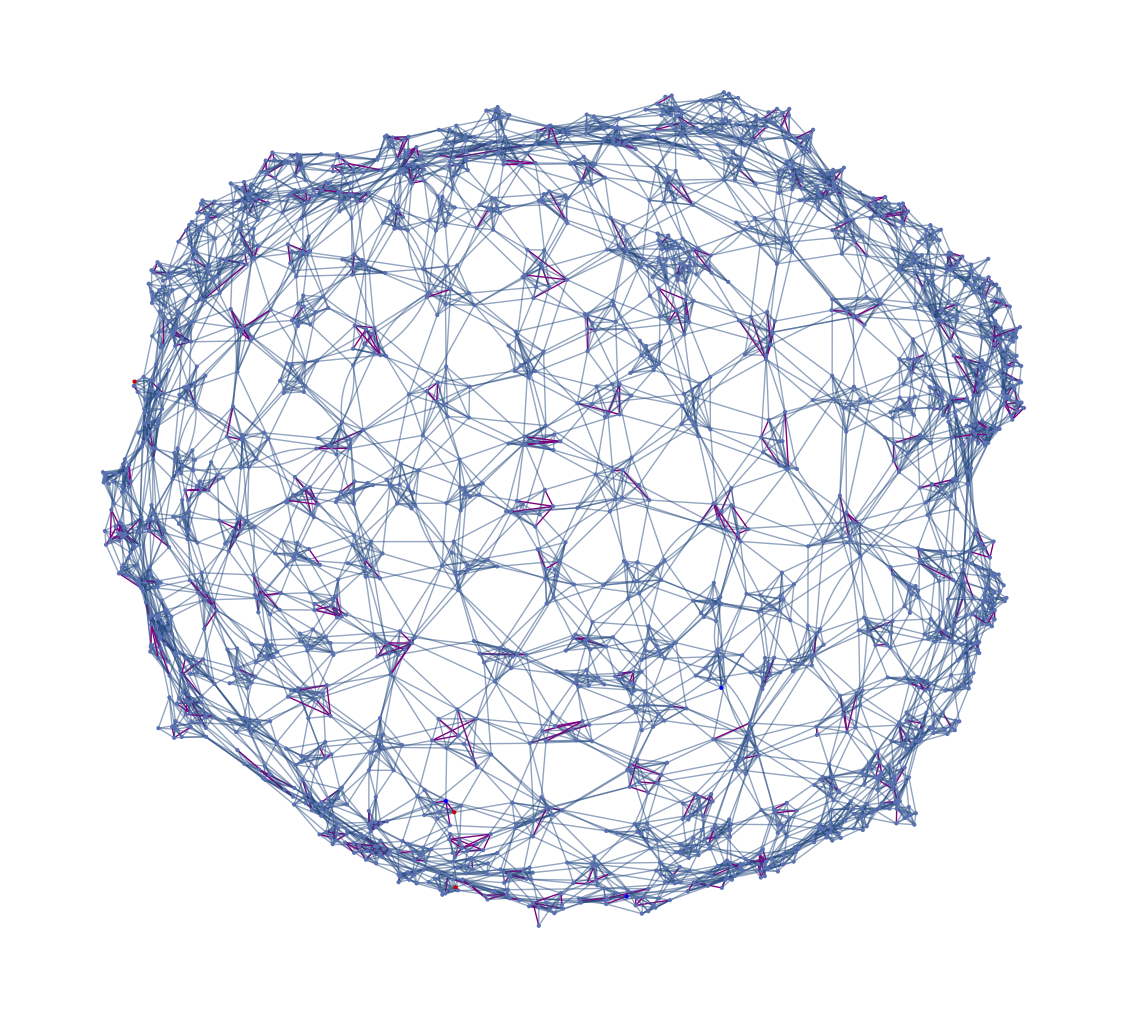

```mathematica
With[{infected=Keys@Select[agentStates1,MatchQ[{"I",_}]]},
HighlightGraph[g1,{infected,Style[UndirectedEdge@@@meetings1,Purple,Thick],
Style[Complement[Flatten[Select[meetings1,IntersectingQ[#,infected]&]],infected],Blue]}]]
```

```mathematica
sims=Association@Table[m->simulate[sims=Association@Table[m->simulate[agentNeighborhoods[g1],
AssociationMap[PearsonDistribution[6, 0.55216,0.98574,0.000011839,1,1]&,VertexList[g1]],
ExponentialDistribution[1/14],10,Infinity],{m,0.05,1,0.01}];agentNeighborhoods[g1],AssociationMap[PearsonDistribution[6, 0.55216,0.98574,0.000011839,1,1]&,VertexList[g1]],ExponentialDistribution[1/14],10,Infinity],{m,0.05,1,0.01}];
```